Info on the notebook:
This notebook uses the BiGONLight package to compute observables in LTB model.
It is structured as follows: 
- model set-up:  give the 4D metric tensor components as input and compute the 3+1 quantities lapse α, shift β^i, spatial metric γ_ij, extrinsic curvature K_ij and the normal vector n^μ;
- geodesic: provide initial position and tangent vector {x^μ, ℓ^μ} as input to find null geodesics;
- parallel transported frame: give the initial conditions for a frame (ϕ^μ)_αthat will be parallel transported along the computed geodesic (we use the SNF, i.e. (ϕ^μ)_α={u^μ,(ϕ^μ)_1,(ϕ^μ)_2, ℓ^μ} with u^μ the four-velocity and (ϕ^μ)_A two orthonormal vectors)
- optical tidal matrix: compute the optical tidal matrix (R^μ)_ρσν ℓ^ρ ℓ^σ in the parallel propagated frame; 
- BGO: compute and solve the Geodesic Deviation Equation for the Bi-local Geodesic Operators along the null geodesic;
- observables: compute the optical observables in the BGO framework: redshift, redshift drift, angular diameter distance, luminosity distance, parallax distance, distance slip, convergence and shear.

Set the current directory as working directory and load the package.

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["bigonlight6`"]
$PreRead=(#/.s_String/;StringMatchQ[s,NumberString]&&Precision@ToExpression@s==MachinePrecision:>s<>"`70."&);
```

a generic direction can be written as 𝓋^μ=𝓋^0∂_0 +ψ(sinχ cosξ ∂_1 +sinχ sinξ ∂_1 +cosχ ∂_3)=(𝓋^0(∂_0))^μ+ψ (N⃗)^μ with respect to the local tetrad ∂_μ . 
In particular for a null direction 𝓋^0=±1 and ψ=1 , while for a timelike direction 𝓋^0=±c γ and ψ=c γ β  where β=vel/c the normalized velocity and γ=1/(√(1-β^2)) the Lorentz factor.

BGO=<<”BGO_data.m”;
totN=<<”geodesic_data.m”;

```mathematica
𝒱[Vt_,lorentz_,direction1_,direction2_]:=
Module[{V0=Vt, γ=lorentz,χ=direction1,ξ=direction2},
V0{1,0,0,0}+γ(Sin[χ]Cos[ξ]{0,1,0,0}+Sin[χ]Sin[ξ]{0,0,1,0}+Cos[χ]{0,0,0,1})
]
```

```mathematica
StandardPlotStyle[size_,sizelegend_,ylabel_,xlabel_,title_,legend_,position_]:=Module[{ft=size,ftL=sizelegend,yL=ylabel,xL=xlabel,pt=title,list=legend,pl=position},
If[ list=={},{FrameLabel->{{yL,""},{xL,""}},Frame->True,FrameTicks->True,FrameStyle->Directive[FontSize->ft],GridLines->Automatic,GridLinesStyle->Directive[Gray,Opacity[0.2],Dashed],PlotLabel->Style[pt,Bold,FontSize->ft]},{FrameLabel->{{yL,""},{xL,""}},Frame->True,FrameTicks->True,FrameStyle->Directive[FontSize->ft],GridLines->Automatic,GridLinesStyle->Directive[Gray,Opacity[0.2],Dashed],PlotLabel->Style[pt,Bold,FontSize->ft],PlotLegends->Placed[LineLegend[Table[Style[list[[m]],FontSize->ftL],{m,1,Length[list]}]],pl]},Print["Error"]]];
```

# LTB

In this notebook we use geometric units G=c=1. This allows us to express mass, length and  time as the same unit. For our convenience, we will express all quantities as dimension-less quantities in units of length L. Therefore, any physical quantity Q^phys=Q^comp L^α where α is a certain exponent and Q^comp is dimensionless. 
L is arbitrary chosen: in particular, we choose to set L such that ℋ_0 L=2 (from Friedman equations, such that η_0==1).
In units of Mpc, we have L=2/ℋ_0=2/(67.36/299792.458[km/(s Mpc) 1/(km/s)])=8901.2 Mpc.
The computational present time is η_0^comp==η_0/L==1

## Units and Parameters

```mathematica
L=2/(H0 Sqrt[Ωm0])/.{H0->67.36/299792.458, Ωm0->1}(*Mpc*);

𝒽0=2/Sqrt[Ωm0]/.{ Ωm0->1};
t0=1;
ti=2/(𝒽0 Sqrt[Ωm0])Sqrt[1/11]/.{ Ωm0->1};
r0=1(*10^-5*)
```

1

```mathematica
L
```

8901.20124703088

```mathematica
param={Ωm0->1, c->1,rb->1/4,tb->1/5};
```

## Model set-up

#### Set up the LTB model

```mathematica
M[r_]:=2/9 r^3
tB[r_]:=tb-1/(1+(r/rb)^2)
ℰ[r_]:=1
```

Φ[t,r]==χ[t,r]^2/2
χ[t,r]^3/6==ℰ[r]^(3/2)(t-tB[r])/M[r]→ χ[t,r]==(6(t-tB[r])/M[r])^(1/3)
Φ[t,r]==χ[t,r]^2/2==(6(t-tB[r])/M[r])^(2/3)/2==((3(t-tB[r])/(1/9 r^3))^(2/3))/2==((3(t-tB[r])/(1/9 r^3))^(2/3))/2==9/2 (t-tB[r])^(2/3)/r^2→
ℛ[t,r]==M[r]/ℰ[r]Φ[t,r]==(2/9 r^3)/1 9/2 (t-tB[r])^(2/3)/r^2==r (t-tB[r])^(2/3)==r (t-tb+1/(1+(r/rb)^2))^(2/3)

```mathematica
ℛ[t_,r_]:=r (t-tb+1/(1+(r/rb)^2))^(2/3)
```

```mathematica
Series[r (t-tb+1/(1+(r/rb)^2))^(2/3),{t,1,3}]
Series[r (t-tb+1/(1+(r/rb)^2))^(2/3),{r,0,3}]
```

r ((r^2+2 rb^2-r^2 tb-rb^2 tb)/(r^2+rb^2))^(2/3)+(2 r ((r^2+2 rb^2-r^2 tb-rb^2 tb)/(r^2+rb^2))^(2/3) (t-1))/(3 (1+1/(1+r^2/rb^2)-tb))-((r ((r^2+2 rb^2-r^2 tb-rb^2 tb)/(r^2+rb^2))^(2/3)) (t-1)^2)/(9 (1+1/(1+r^2/rb^2)-tb)^2)+(4 r ((r^2+2 rb^2-r^2 tb-rb^2 tb)/(r^2+rb^2))^(2/3) (t-1)^3)/(81 (1+1/(1+r^2/rb^2)-tb)^3)+O[t-1]^4

(1+t-tb)^(2/3) r-(2 r^3)/(3 (rb^2 (1+t-tb)^(1/3)))+O[r]^4

```mathematica
(tb-1/(1+(r/rb)^2))/.{rb->Table[i,{i,10^-5,1,(1-10^-5)/9}],tb->t0}
```

{1-1/(1+10000000000 r^2),1-1/(1+(156250000 r^2)/1929321),1-1/(1+(10000000000 r^2)/493861729),1-1/(1+(2500000000 r^2)/277788889),1-1/(1+(400000000 r^2)/79014321),1-1/(1+(625000000 r^2)/192904321),1-1/(1+(10000000000 r^2)/4444488889),1-1/(1+(2500000000 r^2)/1512354321),1-1/(1+(10000000000 r^2)/7901254321),1-1/(1+r^2)}

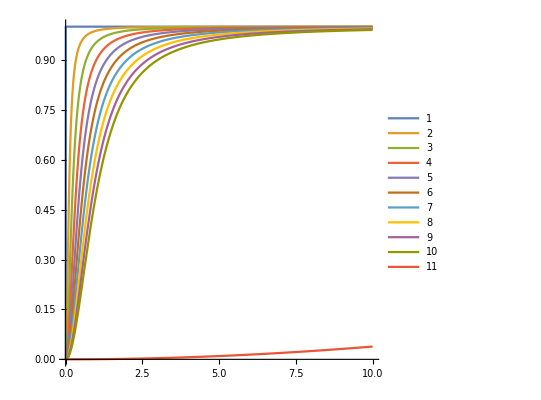

```mathematica
(*Plot3D[r (t-tb+1/(1+(r/rb)^2))^(2/3)/.{rb->5,tb->t0},{r,0,10},{t,0,t0},PlotRange->All,AspectRatio->1]
Plot[tb-1/(1+(r/rb)^2)/.{r->5,tb->t0},{t,0,t0},PlotRange->All,AspectRatio->1,PlotLegends->Automatic]*)
Plot[{1-1/(1+10000000000 r^2),1-1/(1+(156250000 r^2)/1929321),1-1/(1+(10000000000 r^2)/493861729),1-1/(1+(2500000000 r^2)/277788889),1-1/(1+(400000000 r^2)/79014321),1-1/(1+(625000000 r^2)/192904321),1-1/(1+(10000000000 r^2)/4444488889),1-1/(1+(2500000000 r^2)/1512354321),1-1/(1+(10000000000 r^2)/7901254321),1-1/(1+r^2),(1-1/(1+(r/50)^2))},{r,0,10},PlotRange->All,AspectRatio->1,PlotLegends->Automatic]
```

We need to provide the spacetime metric g_μν. 
This can be done in two ways: 
		1)  writing the analytic expression for the metric components g_μν=(g_00 | g_01 | g_02 | g_03
g_10 | g_11 | g_12 | g_13
g_20 | g_21 | g_22 | g_23
g_30 | g_31 | g_32 | g_33) 
		2) import data from a (relativistic) numerical simulation. 
		
In this case, we know the form of the metric g_μν, so we use the first method.

```mathematica
Clear[α,β,g,K,g4,X,V,e,Energy,nd,nu,ℰ,ℛ,x,y,z,η,ϕ]
```

```mathematica
X4={η,r,θ,ϕ};
X={r,θ,ϕ};
V={v1,v2,v3};
e={e1,e2,e3};
Energy={energy, affine};
```

```mathematica
g4={{-1,0,0,0},{0,D[ℛ[η, r], r]^2/(1+2ℰ[r]),0,0},{0,0,(ℛ[η, r])^2,0},{0,0,0,(ℛ[η, r])^2}};
```

```mathematica
solADM=ADM[g4,X4];
α=Evaluate[solADM[[1]]]
β=Evaluate[solADM[[2]]]
g=Evaluate[solADM[[3]]]
K=Evaluate[solADM[[4]]]
nu=Evaluate[solADM[[5]]]
nd=Evaluate[solADM[[6]]]
```

1

{0,0,0}

{{((ℛ^(0,1)[η,r])^2)/(1+2 ℰ[r]),0,0},{0,ℛ[η,r]^2,0},{0,0,ℛ[η,r]^2}}

{{-(ℛ^(0,1)[η,r] ℛ^(1,1)[η,r])/(1+2 ℰ[r]),0,0},{0,-ℛ[η,r] ℛ^(1,0)[η,r],0},{0,0,-ℛ[η,r] ℛ^(1,0)[η,r]}}

{1,0,0,0}

{-1,0,0,0}

```mathematica
αα[τ_]:=α/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];
ββ[τ_]:=β/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];
VV[η_]:=Table[V[[i]][η],{i,1,Length[X]}];
gg[τ_]:=g/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];
gg4[τ_]:=g4/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];
nup[τ_]:=nu/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];
ndown[τ_]:=nd/.Join[{η->τ},Table[X[[i]]-> X[[i]][τ],{i,1,Length[X]}]];

αlup[η_]:=(*EBG[η]*)αα[η] (nup[η]+Flatten[{0,VV[η]}]);
αldown[η_]:=(*EBG[η]*)αα[η](ndown[η]+Flatten[{0,gg[η].VV[η]}]);
```

## Geodesic

```mathematica
geod=GeodesicEquations[X,V,g,K,α,β,η]
```

{r'[η]==v1[η],v1'[η]==(v2[η]^2 (1+2 ℰ[r[η]]) ℛ[η,r[η]])/(ℛ^(0,1)[η,r[η]])+(v3[η]^2 (1+2 ℰ[r[η]]) ℛ[η,r[η]])/(ℛ^(0,1)[η,r[η]])-v1[η]^2 (-ℰ'[r[η]]/(1+2 ℰ[r[η]])+(ℛ^(0,2)[η,r[η]])/(ℛ^(0,1)[η,r[η]]))-(2 v1[η] ℛ^(1,1)[η,r[η]])/(ℛ^(0,1)[η,r[η]])+v1[η] (v2[η]^2 ℛ[η,r[η]] ℛ^(1,0)[η,r[η]]+v3[η]^2 ℛ[η,r[η]] ℛ^(1,0)[η,r[η]]+(v1[η]^2 ℛ^(0,1)[η,r[η]] ℛ^(1,1)[η,r[η]])/(1+2 ℰ[r[η]])),θ'[η]==v2[η],v2'[η]==-(2 v1[η] v2[η] ℛ^(0,1)[η,r[η]])/ℛ[η,r[η]]-(2 v2[η] ℛ^(1,0)[η,r[η]])/ℛ[η,r[η]]+v2[η] (v2[η]^2 ℛ[η,r[η]] ℛ^(1,0)[η,r[η]]+v3[η]^2 ℛ[η,r[η]] ℛ^(1,0)[η,r[η]]+(v1[η]^2 ℛ^(0,1)[η,r[η]] ℛ^(1,1)[η,r[η]])/(1+2 ℰ[r[η]])),ϕ'[η]==v3[η],v3'[η]==-(2 v1[η] v3[η] ℛ^(0,1)[η,r[η]])/ℛ[η,r[η]]-(2 v3[η] ℛ^(1,0)[η,r[η]])/ℛ[η,r[η]]+v3[η] (v2[η]^2 ℛ[η,r[η]] ℛ^(1,0)[η,r[η]]+v3[η]^2 ℛ[η,r[η]] ℛ^(1,0)[η,r[η]]+(v1[η]^2 ℛ^(0,1)[η,r[η]] ℛ^(1,1)[η,r[η]])/(1+2 ℰ[r[η]]))}

```mathematica
enereq=EnergyEquations[g,K,α,β,Energy,X,V,η]
```

{energy'[η]==energy[η] (-v2[η]^2 ℛ[η,r[η]] ℛ^(1,0)[η,r[η]]-v3[η]^2 ℛ[η,r[η]] ℛ^(1,0)[η,r[η]]-(v1[η]^2 ℛ^(0,1)[η,r[η]] ℛ^(1,1)[η,r[η]])/(1+2 ℰ[r[η]])),affine'[η]==1/energy[η]}

```mathematica
ℛ[t_,r_]:=r (t-tb+1/(1+(r/rb)^2))^(2/3)/.param
M[r_]:=2/9 r^3
tB[r_]:=tb-1/(1+(r/rb)^2)/.param
ℰ[r_]:=0
ρ[t_,r_]:=M'[r]/(4π D[ℛ[t,s],s] ℛ[t,r]^2)/.s->r
```

```mathematica
Plot3D[ρ[t,r],{t,ti,t0},{r,10^-5,3},PlotRange->All]
```

-Graphics3D-

### Initial conditions

The initial conditions can be given in two different ways:
1) directly specifying the values or
2) giving the initial direction v^2 and v^3 and use the function InitialConditions[] to compute v^1 such that the geodesic is null.

```mathematica
κ=SetPrecision[(*A[ηin]^-2*)𝒱[-1,1,π/2,0],70]
TimeObject[Now]
```

{-1.,1.,0,0}

10:31:36GMT+2.TimeObject[{10,31,36.050975},TimeZone→2.]

The vector κ^μ must be expressed in 3+1 form κ^μ=E(n^μ+V^μ) where E=-κ^μ n_μ and V^μ=κ^μ/E-n^μ

```mathematica
ϵ=SetPrecision[∑_(i=1)^4 -κ[[i]]nd[[i]]/.{η->t0,r->r0,θ->0,ϕ->0},70]/.param
vi=SetPrecision[Table[(κ[[i]]/ϵ-nu[[i]])/.{η->t0,r->r0,θ->0,ϕ->0},{i,1,4}],70]/.param
```

-1.

{0,-1.,0,0}

```mathematica
substitution={η->t0,r->r0,θ->0,ϕ->0,v2->vi[[3]],v3->vi[[4]]};
```

```mathematica
initialvel1=Flatten[InitialConditions[g,substitution,V,param]]
initialN=(*{x[ETA0]==0,y[ETA0]==0,v2[ETA0]==0,z[ETA0]==0,v3[ETA0]==0,v1[1]==-1}*)Flatten[Join[Table[(substitution[[i,1]][η]/.substitution[[1]])==substitution[[i,2]],{i,2,Length[substitution]}],{(V[[1]][η]/.substitution[[1]])==initialvel1[[1,2]](*-2.5 10^-4*)(*(V[[1]]/.initialvel1[[2]])*)}]]
E0N=ϵ(*α/.η->ηin*)(*ϵ*)
initialenergyN={Energy[[1]][t0]==ϵ,Energy[[2]][t0]==1}
```

{v1→-(51 73^(1/3) 85^(2/3))/3403,v1→(51 73^(1/3) 85^(2/3))/3403}

{r[1]==1,θ[1]==0,ϕ[1]==0,v2[1]==0,v3[1]==0,v1[1]==-(51 73^(1/3) 85^(2/3))/3403}

-1.

{energy[1]==-1.,affine[1]==1}

```mathematica
g.V.V/.Join[{initialvel1[[2]]},substitution]/.param//N
(E0N^2 g4.(nu+Join[{0},V]).(nu+Join[{0},V]))/.Join[{initialvel1[[2]]},substitution]/.param
```

1.

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -1+(221085 73^(2/3) 85^(1/3) ((73/85)^(2/3)-(64 (5/73)^(1/3))/(51 17^(2/3)))^2)/11580409.

0.

### Solve the equations numerically, given the functions in the metric explicitly

```mathematica
AbsoluteTiming[geodesicN=Flatten[SolveGeodesic[geod,initialN,X,V,param,η,ti,t0,"SS",80,80,10,5]]]
```

{275.83,{r→InterpolatingFunction[{{0.30151134457776362264681206697006242581155350414448669064169837691968042205536762, 1.0000000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>],θ→InterpolatingFunction[{{0.30151134457776362264681206697006242581155350414448669064169837691968042205536762, 1.0000000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>],ϕ→InterpolatingFunction[{{0.30151134457776362264681206697006242581155350414448669064169837691968042205536762, 1.0000000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>],v1→InterpolatingFunction[{{0.30151134457776362264681206697006242581155350414448669064169837691968042205536762, 1.0000000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>],v2→InterpolatingFunction[{{0.30151134457776362264681206697006242581155350414448669064169837691968042205536762, 1.0000000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>],v3→InterpolatingFunction[{{0.30151134457776362264681206697006242581155350414448669064169837691968042205536762, 1.0000000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>]}}

```mathematica
AbsoluteTiming[enerN=Flatten[SolveEnergy[enereq,initialenergyN,Energy,geodesicN,param,η,ti,t0,"SS",80,80,10,10]]]
```

NDSolve::precw: The precision of the differential equation ({{energy'[η]==energy[η] (-4/3 (InterpolatingFunction[«5»][«1»])^2 (InterpolatingFunction[«5»][«1»])^2 Plus[«3»]^(1/3)-(InterpolatingFunction[«5»][«1»])^2 (Times[«4»]+Times[«2»]) (Times[«4»]+Power[«2»])),affine'[η]==1/energy[η],energy[1]==-1.,affine[1]==1},{},{},{},{}}) is less than WorkingPrecision (80.).

InterpolatingFunction::dmval: Input value {1.0000000000000000000000000000000000000000999999999999997278387939275479556026274} lies outside the range of data in the interpolating function. Extrapolation will be used.

{231.002,{energy→InterpolatingFunction[{{0.30151134457776362264681206697006242581155350414448669064169837691968042205536762, 1.0000000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>],affine→InterpolatingFunction[{{0.30151134457776362264681206697006242581155350414448669064169837691968042205536762, 1.0000000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>]}}

Test that the constraint conditions are satisfied for all the evolution

```mathematica
geodesic=Join[geodesicN,enerN];
```

Note: 	the solution can be saved in a file as: geodesic >> “file_name.m”.
		Similarly, “.m” files can be imported using the syntax:  geodesic =<<”file_name.m”

```mathematica
geodesic=<<"Sz_geodesic_OtoS_onX.m";
```

Test the null condition along the geodesic

10:40:53GMT+2.TimeObject[{10,40,53.091842},TimeZone→2.]

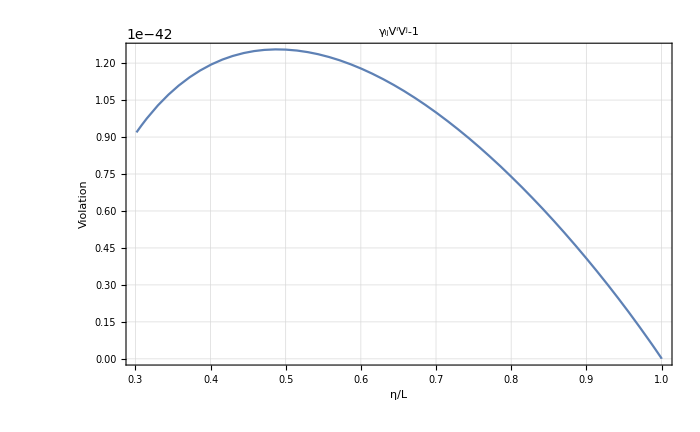

-Graphics-

```mathematica
TimeObject[Now]
EN[η_]:=energy[η]/.geodesic;
lupN[η_]:=EN[η](nup[η]+Flatten[{0,VV[η]}]);
ldownN[η_]:=EN[η](ndown[η]+Flatten[{0,gg[η].VV[η]}]);
Plot[Evaluate[{gg[η].VV[η].VV[η]-1}/.geodesic/.param], {η, ti,t0},PlotRange->All,WorkingPrecision->60,ImageSize->700,Evaluate[StandardPlotStyle[16,24,"Violation","η/L","γ_ijV^iV^j-1",{},{}]]]
Plot[Evaluate[{gg4[η].lupN[η].lupN[η],lupN[η].ldownN[η]}/.geodesic/.param], {η, ti,t0},PlotRange->All,WorkingPrecision->60,ImageSize->700,Evaluate[StandardPlotStyle[16,24,"Violation","η/L","g_μνℓ^μℓ^ν",{"up-up","up-down"},{1,0.5}]]]
```

```mathematica
ℓic=EN[t0](nu+Join[{0},V])/.Join[{initialvel1[[2]]},substitution]/.param
```

{-1.,-1.210863340341390258909436100859262927622622702613426757334455192083995070765857,0,0}

```mathematica
Join[geodesicN,enerN]>>"LTB_geodesic_onR.m";
```

### Compute the redshift

The  redshift is defined as z+1==(g_μν u^μ ℓ^ν|_𝒮)/(g_μν u^μ ℓ^ν|_𝒪). 
In 3+1, decomposing u^μ==Γ(n^μ+U^μ) and ℓ^μ=ℰ(n^μ+V^μ), the redshift becomes: z+1==ℰ_𝒮/ℰ_𝒪(1-γ_ij V^i U^j|_𝒮)/(1-γ_ij V^i U^j|_𝒪)((1-γ_ij U^i U^j|_𝒮)/(1-γ_ij U^i U^j|_𝒪))^(1/2). In synchronous-comoving coordinates U^i==0 and the redshift simplifies to z+1==ℰ_𝒮/ℰ_𝒪

```mathematica
ZN[η_]=EN[η]/EN[t0]-1;
```

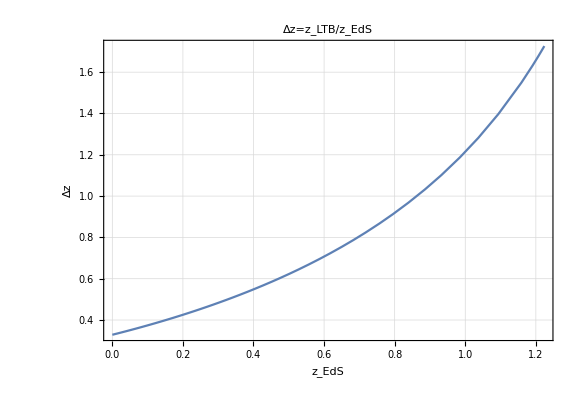

```mathematica
ParametricPlot[{(t0^(2/3)/η^(2/3)-1),ZN[η]/(t0^(2/3)/η^(2/3)-1)-1}, {η, ti,t0},PlotRange->All,AspectRatio->0.7,ImageSize->Large, WorkingPrecision->40,Evaluate[StandardPlotStyle[16,24,"Δz","z_EdS","Δz=z_LTB/z_EdS",{},{}]]]
```

Analytic expression for the geodesic eq in LTB: consider radial geodesic

```mathematica
Γi=Christoffel[{{-1,0,0,0},{0,D[ℛa[η, r], r]^2/(1+2ℰa[r]),0,0},{0,0,(ℛa[η, r])^2,0},{0,0,0,(ℛa[η, r])^2}},X4];
```

```mathematica
ℓμ={ℓ0,ℓ1,0,0};
dℓμ={dℓ0,dℓ1,dℓ2,dℓ3};
Table[dℓμ[[i1]]==∑_(s1=1)^4 ∑_(s2=1)^4 Γi[[i1,s1,s2]]ℓμ[[s1]]ℓμ[[s2]],{i1,1,4}]//Simplify//MatrixForm
```

(dℓ0==(ℓ1^2 ℛa^(0,1)[η,r] ℛa^(1,1)[η,r])/(1+2 ℰa[r])
dℓ1==ℓ1 (-(ℓ1 ℰa'[r])/(1+2 ℰa[r])+(ℓ1 ℛa^(0,2)[η,r]+2 ℓ0 ℛa^(1,1)[η,r])/(ℛa^(0,1)[η,r]))
dℓ2==0
dℓ3==0)

Compute the redshift in LTB (standard method)

```mathematica
DtrR[t_,r_]:=D[ℛ[u,s],u,s]/.{u->t,s->r}
DrR[t_,r_]:=D[ℛ[u,s],s]/.{u->t,s->r}
```

```mathematica
ℓ0sol=NDSolve[{es'[η]==-es[η] DtrR[η,r[η]]/DrR[η,r[η]]/.geodesic,es[t0]==-1}/.param,es,{η,ti,t0},WorkingPrecision->100,PrecisionGoal->100,InterpolationOrder->10,Method->"StiffnessSwitching",MaxSteps->10^10]
```

InterpolatingFunction::dmval: Input value {1.000000000000000000000000000000000000000000000000010000000000000112836029217955433554820745042690168} lies outside the range of data in the interpolating function. Extrapolation will be used.

{{es→InterpolatingFunction[…]}}

```mathematica
ℓ0LTB[s_]:=es[s]/.Flatten[ℓ0sol]
```

```mathematica
Zbg[η_]=t0^(2/3)/η^(2/3)-1;
ZLTB[η_]=SetPrecision[ℓ0LTB[η]/ℓ0LTB[t0]-1,60];
```

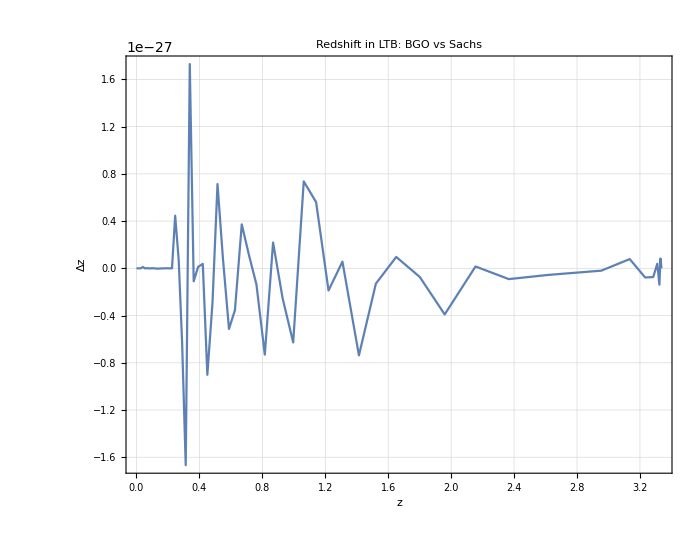

```mathematica
ParametricPlot[{ZN[η],(ZN[η]/ZLTB[η]-1)},{η,ti,t0},PlotRange->All(*{{-0.4, 10.4},{-10,10}}*),Evaluate[StandardPlotStyle[18,24,"Δz","z","Redshift in LTB: BGO vs Sachs",{},{}]],AspectRatio->0.8, ImageSize->700,WorkingPrecision->50]
```

Compute the null geodesic

```mathematica
trajectoryN[η_]:=Flatten[{r[η]Sin[θ[η]]Cos[ϕ[η]] ,r[η]Sin[θ[η]]Sin[ϕ[η]] ,r[η]Cos[θ[η]] }/.geodesic/.param];
Show[ParametricPlot3D[trajectoryN[η],{η,ti,t0},PlotRange->All(*{{-20,20},{- 20,20},{-20,20}}*), ImageSize->700, ViewPoint->{0,0,Infinity}, AxesLabel->{"X/L","Y/L","Z/L"}]/.Line[x_]:>Sequence[Arrowheads[Table[.02,{100/10}]],Arrow@Line[x]] ]
```

-Graphics3D-

REMEMBER: consider that X^μ and V^μ are expressed in the comoving reference frame (e^μ)_i and this must be taken into account if we want to understand the numerical results. So the 3-velocity dx^i/dt=α V^i-β^i

## Parallel transport of a frame

```mathematica
Clear[transport2,vecbcframe,soltrans2,soldeviation,solGDE,tot1,tot2,totl,totu,Cu,Cl,Cf1,Cf2,Pu,Pl,P1,P2,F,F0,EE,EE0,OPT,ξ,ξA,ξbc,Ξ,ξ4,DA,DAbc,DAsolGDE,JMAP,frame,frame0]
```

```mathematica
frame0={fu0,f10,f20,fl0};
frame={{fu1,fu2,fu3},{f11,f12,f13},{f21,f22,f23},{fl1,fl2,fl3}};
TimeObject[Now]
```

10:47:06GMT+2.TimeObject[{10,47,6.924151},TimeZone→2.]

### set-up the initial conditions for the SNF

```mathematica
Γl=1;
Β=0;
u[τ_]:=SetPrecision[(Γl/Sqrt[-g4[[1,1]]]{1,0,0,0}+Γl Β(Cos[0]Sin[π/2] 1/Sqrt[g4[[2,2]]]{0,1,0,0}+Sin[0]Sin[π/2] 1/Sqrt[g4[[3,3]]]{0,0,1,0}+Cos[π/2] 1/Sqrt[g4[[4,4]]]{0,0,0,1})),100]/.η->τ;
(*u[η_]:=SetPrecision[{1,0,0,0},50]*)
u[t0]//N
u[ti]//N
```

{1.,0.,0.,0.}

{1.,0.,0.,0.}

```mathematica
gg4[t0].u[t0].lupN[t0]/.Join[geodesic,param]
gg4[t0].u[t0].u[t0]/.η->ti
```

1.

-1.

Assuming f_1^μ=OverTilde[f_1]^μ+A u^μ+B k^μ and f_2^μ=OverTilde[f_2]^μ+C u^μ+D k^μ+E f_1^μ, the relations between the vector of the SNF can used to determine the constants A, B, C, D and E.

```mathematica
p1={0,0,1,0};
p2={0,0,0,1};
```

```mathematica
𝒻1=Re[(p1-(gg4[t].p1.lupN[t])/(gg4[t].lupN[t].u[t])u[t]-1/(gg4[t].lupN[t].u[t])((gg4[t].p1.lupN[t])/(gg4[t].lupN[t].u[t])+gg4[t].p1.u[t])lupN[t])/.Join[geodesic,param]/.t->t0]
s1=𝒻1/Sqrt[gg4[t0].𝒻1.𝒻1]/.Join[geodesic,param]/.t->t0
(gg4[t0].s1.s1)/.Join[geodesic,param]/.t->t0
```

{0,0,1,0}

{0,0,1.106786985544386529967448576745654510529085430296398403225665060075701108196672,0}

1.

```mathematica
𝒻2=Re[(p2-(gg4[t].p2.lupN[t])/(gg4[t].lupN[t].u[t])u[t]-1/(gg4[t].lupN[t].u[t])((gg4[t].p2.lupN[t])/(gg4[t].lupN[t].u[t])+gg4[t].p2.u[t])lupN[t]-(gg4[t].p2.s1)s1)/.Join[geodesic,param]/.t->t0]
s2=𝒻2/Sqrt[gg4[t0].𝒻2.𝒻2]/.Join[geodesic,param]/.t->t0
(gg4[t0].s2.s2)/.Join[geodesic,param]/.t->t0
```

{0,0,0,1}

{0,0,0,1.106786985544386529967448576745654510529085430296398403225665060075701108196672}

1.

Initial conditions for the SN frame

```mathematica
(*u={1/A[η],0,0,0}=> fu0=α u^0 , fu^i=u^i+fu0 β^i/α;
f1=s1=> f10=α s1^0, f1^i=s1^i+f10 β^i/α;
f2=s2=> f20=α s2^0, f2^i=s2^i+f20 β^i/α;
ENW[η_]:=First[Evaluate[energy[η]/.enerNW]];
k[η_]:= Evaluate[(ENW[η](nup[η]+Flatten[{0,VV[η]}]))/.Join[geodesicNW]];
k => fl0=α k^0, fl^i=k^i+fl0 β^i/α ;*)
```

```mathematica
geodesicN=geodesic;
```

```mathematica
fu0in=(*Cu=*)SetPrecision[((-ndown[t].u[t])/.geodesicN/.param)/.t->t0,50];
fuin=(*fu^μ=*)SetPrecision[((u[t]-(-ndown[t].u[t]) nup[t])/.geodesicN/.param)/.t->t0,50];

f10in=(*C1=*)SetPrecision[((-ndown[t].s1)/.geodesicN/.param)/.t->t0,50];
f1in=(*Subscript[f, 1]^μ=*)SetPrecision[((s1-(-ndown[t].s1) nup[t])/.geodesicN/.param)/.t->t0,50];

f20in=(*C2=*)SetPrecision[((-ndown[t].s2)/.geodesicN/.param)/.t->t0,50];
f2in=(*Subscript[f, 2]^μ=*)SetPrecision[((s2-(-ndown[t].s2) nup[t])/.geodesicN/.param)/.t->t0,50];

fl0in=(*Ck=*)SetPrecision[((-ndown[t].lupN[t])/.geodesicN/.param)/.t->t0,50];(*SetPrecision[A[ηin],∞];*)
flin=(*fk^μ=*)SetPrecision[((lupN[t]-(fl0in) nup[t])/.geodesicN/.param)/.t->t0,50];
```

### Parallel transport the SNF

```mathematica
initialframeN={{fu0[t0]==fu0in,fu1[t0]==fuin[[2]],fu2[t0]==fuin[[3]] ,fu3[t0]==fuin[[4]]},{f10[t0]==f10in,f11[t0]==f1in[[2]],f12[t0]==f1in[[3]],f13[t0]==f1in[[4]]},{f20[t0]==f20in,f21[t0]==f2in[[2]],f22[t0]==f2in[[3]],f23[t0]==f2in[[4]] },{fl0[t0]==fl0in,fl1[t0]==flin[[2]],fl2[t0]==flin[[3]],fl3[t0]==flin[[4]]}};
```

```mathematica
initialframeN//N
```

{{fu0[1.]==1.,fu1[1.]==0.,fu2[1.]==0.,fu3[1.]==0.},{f10[1.]==0.,f11[1.]==0.,f12[1.]==100000.,f13[1.]==0.},{f20[1.]==0.,f21[1.]==0.,f22[1.]==0.,f23[1.]==100000.},{fl0[1.]==-1.,fl1[1.]==-1.,fl2[1.]==0.,fl3[1.]==0.}}

```mathematica
Timing[soltransN=Flatten[PTransportedFrame[g,K,α,β,geodesicN,initialframeN,frame,frame0,param,η,ti,t0,"SS",70,70,10,5]]]
```

NDSolve::precw: The precision of the differential equation ({«1»}) is less than WorkingPrecision (70.).

InterpolatingFunction::dmval: Input value {1.000000000000000000000000000000000010000000000000000078575451945823803} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::precw: The precision of the differential equation ({«1»}) is less than WorkingPrecision (70.).

InterpolatingFunction::dmval: Input value {1.000000000000000000000000000000000010000000000000000078575451945823803} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{f20'[η]==-2/3 f22[η] «1» (InterpolatingFunction[{«1»},{«13»},{«1»},{«28866»},{«1»}][η])^2 (-1/5+η+Power[«2»])^(1/3)-2/3 f23[η] InterpolatingFunction[{{«2»}},«3»,{{«2»}}][η] (InterpolatingFunction[«1»][η])^2 (-1/5+η+Power[«2»])^(1/3)-f21[η] «1» (64/9 Power[«2»] Power[«2»] Power[«2»]+2/3 Power[«2»]) (-64/3 Power[«2»] Power[«2»] Power[«2»]+Plus[«3»]^(2/3)),«7»},«3»,{}}) is less than WorkingPrecision (70.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

{556.381,{fu1→InterpolatingFunction[{{0.3015113445777636226468120669700624258115535041444866906416983769196804, 1.000000000000000000000000000000000000000000000000000000000000000000000}}, <>],fu2→InterpolatingFunction[{{0.3015113445777636226468120669700624258115535041444866906416983769196804, 1.000000000000000000000000000000000000000000000000000000000000000000000}}, <>],fu3→InterpolatingFunction[{{0.3015113445777636226468120669700624258115535041444866906416983769196804, 1.000000000000000000000000000000000000000000000000000000000000000000000}}, <>],fu0→InterpolatingFunction[{{0.3015113445777636226468120669700624258115535041444866906416983769196804, 1.000000000000000000000000000000000000000000000000000000000000000000000}}, <>],f11→InterpolatingFunction[{{0.3015113445777636226468120669700624258115535041444866906416983769196804, 1.000000000000000000000000000000000000000000000000000000000000000000000}}, <>],f12→InterpolatingFunction[{{0.3015113445777636226468120669700624258115535041444866906416983769196804, 1.000000000000000000000000000000000000000000000000000000000000000000000}}, <>],f13→InterpolatingFunction[{{0.3015113445777636226468120669700624258115535041444866906416983769196804, 1.000000000000000000000000000000000000000000000000000000000000000000000}}, <>],f10→InterpolatingFunction[{{0.3015113445777636226468120669700624258115535041444866906416983769196804, 1.000000000000000000000000000000000000000000000000000000000000000000000}}, <>],f21→InterpolatingFunction[{{0.3015113445777636226468120669700624258115535041444866906416983769196804, 1.000000000000000000000000000000000000000000000000000000000000000000000}}, <>],f22→InterpolatingFunction[{{0.3015113445777636226468120669700624258115535041444866906416983769196804, 1.000000000000000000000000000000000000000000000000000000000000000000000}}, <>],f23→InterpolatingFunction[{{0.3015113445777636226468120669700624258115535041444866906416983769196804, 1.000000000000000000000000000000000000000000000000000000000000000000000}}, <>],f20→InterpolatingFunction[{{0.3015113445777636226468120669700624258115535041444866906416983769196804, 1.000000000000000000000000000000000000000000000000000000000000000000000}}, <>],fl1→InterpolatingFunction[{{0.3015113445777636226468120669700624258115535041444866906416983769196804, 1.000000000000000000000000000000000000000000000000000000000000000000000}}, <>],fl2→InterpolatingFunction[{{0.3015113445777636226468120669700624258115535041444866906416983769196804, 1.000000000000000000000000000000000000000000000000000000000000000000000}}, <>],fl3→InterpolatingFunction[{{0.3015113445777636226468120669700624258115535041444866906416983769196804, 1.000000000000000000000000000000000000000000000000000000000000000000000}}, <>],fl0→InterpolatingFunction[{{0.3015113445777636226468120669700624258115535041444866906416983769196804, 1.000000000000000000000000000000000000000000000000000000000000000000000}}, <>]}}

```mathematica
totN=Flatten[Join[Flatten[soltransN],geodesic]];
```

```mathematica
(*totN=Flatten[Join[Flatten[soltransN],geodesicN]];*)
Cu[η_]:=fu0[η];
Cf1[η_]:=f10[η];
Cf2[η_]:=f20[η];
Cl[η_]:=fl0[η];
Pu[η_]:={fu1[η],fu2[η],fu3[η]};
P1[η_]:={f11[η],f12[η],f13[η]};
P2[η_]:={f21[η],f22[η],f23[η]};
Pl[η_]:={fl1[η],fl2[η],fl3[η]};
```

```mathematica
Show[ParametricPlot3D[trajectoryN[η],{η,ti,t0},PlotRange->{{-2,2},{-2,2},{-2,2}}]/.Line[x_]:>Sequence[Arrowheads[Table[.02,{100/10}]],Arrow@Line[x]] ,Graphics3D[{{Red,Arrowheads[0.02],Table[Arrow[{trajectoryN[η],(trajectoryN[η]+(Pu[η]/.totN))}],{η,ti,t0,0.05}]},{Green,Arrowheads[0.02],Table[Arrow[{trajectoryN[η],(trajectoryN[η]+(P1[η]/.totN))}],{η,ti,t0,0.05}]},{Blue,Arrowheads[0.02],Table[Arrow[{trajectoryN[η],(trajectoryN[η]+(P2[η]/.totN))}],{η,ti,t0,0.05}]},{Black,Arrowheads[0.02],Table[Arrow[{trajectoryN[η],(trajectoryN[η]+(Pl[η]/.totN))}],{η,ti,t0,0.05}]}}],Graphics3D[Sphere[{0,0,0},0.05]] , ImageSize->700,ViewPoint->{0,100,10},AxesLabel->{x,y,z},AxesStyle->Directive[Red,12]]
TimeObject[Now]
```

-Graphics3D-

11:37:25GMT+2.TimeObject[{11,37,25.894851},TimeZone→2.]

### Define the induced metric of the SNF “h”

```mathematica
Clear[F,F0,EE,EE0,Q,h]
```

```mathematica
(*((((gg4[ETA0].(Evaluate[Cu[ETA0]nup[ETA0]+Flatten[{0, Pu[ETA0]}]]).(Evaluate[Cl[ETA0]nup[ETA0]+Flatten[{0, Pl[ETA0]}]]))))/.totBG/.param)*)Q=Re[((gg4[t0].(Evaluate[Cu[t0]nup[t0]+Flatten[{0, Pu[t0]}]]).(Evaluate[Cl[t0]nup[t0]+Flatten[{0, Pl[t0]}]]))/.totN/.param)]
h={{-1,0,0,Q},{0,1,0,0},{0,0,1,0},{Q,0,0,0}};
Ih=Inverse[h];
```

1.

```mathematica
F[t_]:={{Pu[t][[1]],P1[t][[1]],P2[t][[1]],Pl[t][[1]]},{Pu[t][[2]],P1[t][[2]],P2[t][[2]],Pl[t][[2]]},{Pu[t][[3]],P1[t][[3]],P2[t][[3]],Pl[t][[3]]}};
F0[t_]:={Cu[t],Cf1[t],Cf2[t],Cl[t]};
TimeObject[Now]
```

11:37:30GMT+2.TimeObject[{11,37,30.545097},TimeZone→2.]

```mathematica
totN>>"LTB_ptSNF_onR.m"
```

#### Check SNF

-0.57735026630287451474075727918495279118

```mathematica
(gg4[t].u[t].s1)/.Join[geodesic,param]/.t->t0
(gg4[t].u[t].s2)/.Join[geodesic,param]/.t->t0
(gg4[t].lupN[t].s1)/.Join[geodesic,param]/.t->t0
(gg4[t].lupN[t].s2)/.Join[geodesic,param]/.t->t0
(gg4[t].s1.s2)/.Join[geodesic,param]/.t->t0
1111111111111111111111111111111111111111111111111111111111111
(gg4[t].s1.s1)/.Join[geodesic,param]/.t->t0
(gg4[t].s2.s2)/.Join[geodesic,param]/.t->t0
(gg4[t].lupN[t].u[t])/.Join[geodesic,param]/.t->t0
(gg4[t].u[t].u[t])/.Join[geodesic,param]/.t->t0
(gg4[t].lupN[t].lupN[t])/.Join[geodesic,param]/.t->t0
```

0

0

0

«2 more identical outputs»

1111111111111111111111111111111111111111111111111111111111111

1.

1.

1.

-1.

0.

```mathematica
Check of the relations: u^μ Subscript[u, μ]=-1,f1^μ Subscript[f1, μ]=1,f2^μ Subscript[f2, μ]=1,k^μ Subscript[k, μ]=0
```

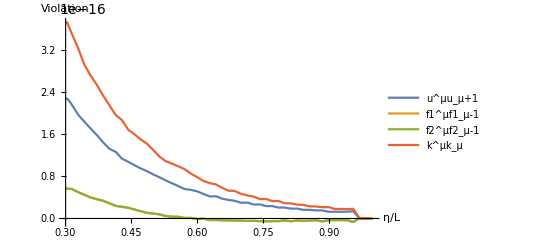

```mathematica
Plot[{(gg4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]).(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]])+1)/.totN/.param,(gg4[η].(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]).(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]])-1)/.totN/.param,(gg4[η].(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]).(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]])-1)/.totN/.param,(gg4[η].(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]).(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]))/.totN/.param},{η,ti,t0},AxesLabel->{"η/L","Violation"},PlotLegends->{"u^μu_μ+1","f1^μf1_μ-1","f2^μf2_μ-1","k^μk_μ"},PlotRange->All(*{-10^-6,10^-6}*),WorkingPrecision->30]
```

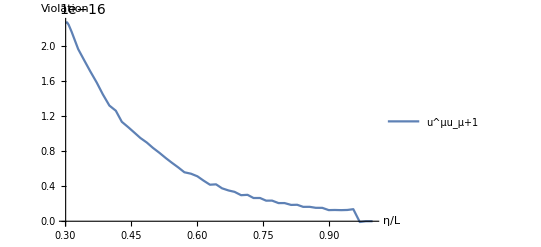

```mathematica
Plot[(gg4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]).(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]])+1)/.totN/.param,{η,ti,t0},AxesLabel->{"η/L","Violation"},PlotLegends->{"u^μu_μ+1","f1^μf1_μ-1","f2^μf2_μ-1","k^μk_μ"},PlotRange->All,WorkingPrecision->30]
```

```mathematica
Check of the relations: u^μ Subscript[f1, μ]=0,u^μ Subscript[f2, μ]=0,k^μ Subscript[f1, μ]=0,k^μ Subscript[f2, μ]=0
```

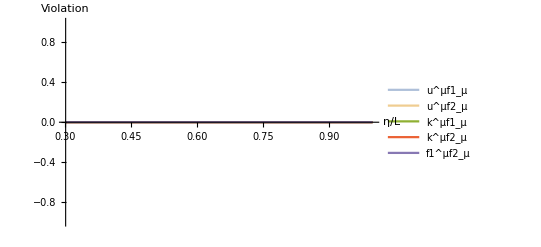

```mathematica
Plot[{(gg4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]).(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]))/.totN/.param,(gg4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]).(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]))/.totN/.param,(gg4[η].(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]).(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]))/.totN/.param,(gg4[η].(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]]).(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]))/.totN/.param,(gg4[η].(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]).(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]]))/.totN/.param},{η,ti,t0},AxesLabel->{"η/L","Violation"},PlotLegends->{"u^μf1_μ","u^μf2_μ","k^μf1_μ","k^μf2_μ","f1^μf2_μ"},PlotRange->All(*{{tin,t0},{-10^-8,10^-8}}*),WorkingPrecision->30,PlotStyle->{Opacity[.5],Opacity[.5],Thick,Thick,Thick}]
```

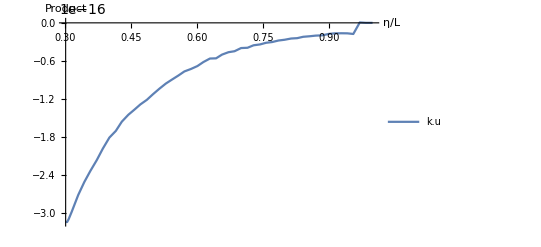

```mathematica
Plot[((((gg4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]).(Evaluate[Cl[η]nup[η]+Flatten[{0, Pl[η]}]])))/((gg4[t0].(Evaluate[Cu[t0]nup[t0]+Flatten[{0, Pu[t0]}]]).(Evaluate[Cl[t0]nup[t0]+Flatten[{0, Pl[t0]}]]))))/.totN/.param)-1,{η,ti,t0},AxesLabel->{"η/L","Product"},PlotLegends->{"k.u"},PlotRange->All,WorkingPrecision->30]
```

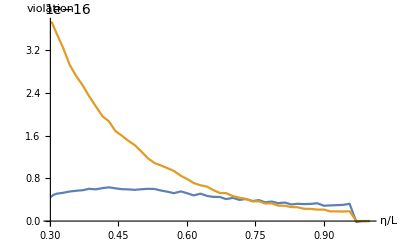

```mathematica
Plot[Evaluate[{(gg[η].VV[η].VV[η]-1),( gg[η].Pl[η].Pl[η]-Cl[η]^2) (*( (gg[η].Pl[η].Pl[η]-Cl[η]^2)/Cl[η]^2) *)}/.totN/.param], {η, ti,t0},PlotRange->Full,AxesLabel->{Style["η/L",Large],Style["violation",Large]},WorkingPrecision->30]
```

## Optical Tidal Matrix

```mathematica
Clear[ℛ,ℰ]
TimeObject[Now]
```

11:38:09GMT+2.TimeObject[{11,38,9.302997},TimeZone→2.]

```mathematica
Timing[OPT=OpticalTidalMatrix[X,V,frame,frame0,Q,g,K,α,β,η]//Simplify;]
```

{2.51487,Null}

```mathematica
OPT//N//MatrixForm
```

(0. | 0. | 0. | 0.
-1. f13[η] fu3[η] v2[η]^2 A'[η]^2+f13[η] fu2[η] v2[η] v3[η] A'[η]^2+f12[η] fu3[η] v2[η] v3[η] A'[η]^2-1. f12[η] fu2[η] v3[η]^2 A'[η]^2+((f12[η]-1. f10[η] v2[η]) (-1. fu2[η]+fu0[η] v2[η]) (A'[η]^2-1. A[η] A''[η])+(f13[η]-1. f10[η] v3[η]) (-1. fu3[η]+fu0[η] v3[η]) (A'[η]^2-1. A[η] A''[η])+(f11[η]-1. f10[η] v1[η]) (-1. fu1[η]+fu0[η] v1[η]) (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (𝒜[x[η],y[η],z[η]] (A'[η]^2-1. A[η] A''[η])+ℱ[η,x[η]] (A'[η]^2-1. A[η] A''[η])-1. A[η] (A'[η] ℱ^(1,0)[η,x[η]]+A[η] ℱ^(2,0)[η,x[η]])))/A[η]^2+f13[η] fu1[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f11[η] fu3[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f13[η] fu3[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f11[η] fu1[η] v3[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+A[η]^2 f13[η] fu2[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+A[η]^2 f12[η] fu3[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f13[η] fu1[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f11[η] fu3[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f12[η] fu1[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f11[η] fu2[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+2. A[η]^2 f11[η] fu1[η] v2[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+f12[η] fu1[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f11[η] fu2[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f12[η] fu2[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f11[η] fu1[η] v2[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]]) | -1. f13[η]^2 v2[η]^2 A'[η]^2+2. f12[η] f13[η] v2[η] v3[η] A'[η]^2-1. f12[η]^2 v3[η]^2 A'[η]^2-(1. ((f12[η]-1. f10[η] v2[η])^2 (A'[η]^2-1. A[η] A''[η])+(f13[η]-1. f10[η] v3[η])^2 (A'[η]^2-1. A[η] A''[η])+(f11[η]-1. f10[η] v1[η])^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (𝒜[x[η],y[η],z[η]] (A'[η]^2-1. A[η] A''[η])+ℱ[η,x[η]] (A'[η]^2-1. A[η] A''[η])-1. A[η] (A'[η] ℱ^(1,0)[η,x[η]]+A[η] ℱ^(2,0)[η,x[η]]))))/A[η]^2+2. f11[η] f13[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f13[η]^2 v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f11[η]^2 v3[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+2. A[η]^2 f12[η] f13[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-2. A[η]^2 f11[η] f13[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-2. A[η]^2 f11[η] f12[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+2. A[η]^2 f11[η]^2 v2[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+2. f11[η] f12[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f12[η]^2 v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f11[η]^2 v2[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]]) | -1. f13[η] f23[η] v2[η]^2 A'[η]^2+f13[η] f22[η] v2[η] v3[η] A'[η]^2+f12[η] f23[η] v2[η] v3[η] A'[η]^2-1. f12[η] f22[η] v3[η]^2 A'[η]^2+((f12[η]-1. f10[η] v2[η]) (-1. f22[η]+f20[η] v2[η]) (A'[η]^2-1. A[η] A''[η])+(f13[η]-1. f10[η] v3[η]) (-1. f23[η]+f20[η] v3[η]) (A'[η]^2-1. A[η] A''[η])+(f11[η]-1. f10[η] v1[η]) (-1. f21[η]+f20[η] v1[η]) (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (𝒜[x[η],y[η],z[η]] (A'[η]^2-1. A[η] A''[η])+ℱ[η,x[η]] (A'[η]^2-1. A[η] A''[η])-1. A[η] (A'[η] ℱ^(1,0)[η,x[η]]+A[η] ℱ^(2,0)[η,x[η]])))/A[η]^2+f13[η] f21[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f11[η] f23[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f13[η] f23[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f11[η] f21[η] v3[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+A[η]^2 f13[η] f22[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+A[η]^2 f12[η] f23[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f13[η] f21[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f11[η] f23[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f12[η] f21[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f11[η] f22[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+2. A[η]^2 f11[η] f21[η] v2[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+f12[η] f21[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f11[η] f22[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f12[η] f22[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f11[η] f21[η] v2[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]]) | 0.
-1. f23[η] fu3[η] v2[η]^2 A'[η]^2+f23[η] fu2[η] v2[η] v3[η] A'[η]^2+f22[η] fu3[η] v2[η] v3[η] A'[η]^2-1. f22[η] fu2[η] v3[η]^2 A'[η]^2+((f22[η]-1. f20[η] v2[η]) (-1. fu2[η]+fu0[η] v2[η]) (A'[η]^2-1. A[η] A''[η])+(f23[η]-1. f20[η] v3[η]) (-1. fu3[η]+fu0[η] v3[η]) (A'[η]^2-1. A[η] A''[η])+(f21[η]-1. f20[η] v1[η]) (-1. fu1[η]+fu0[η] v1[η]) (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (𝒜[x[η],y[η],z[η]] (A'[η]^2-1. A[η] A''[η])+ℱ[η,x[η]] (A'[η]^2-1. A[η] A''[η])-1. A[η] (A'[η] ℱ^(1,0)[η,x[η]]+A[η] ℱ^(2,0)[η,x[η]])))/A[η]^2+f23[η] fu1[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f21[η] fu3[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f23[η] fu3[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f21[η] fu1[η] v3[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+A[η]^2 f23[η] fu2[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+A[η]^2 f22[η] fu3[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f23[η] fu1[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f21[η] fu3[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f22[η] fu1[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f21[η] fu2[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+2. A[η]^2 f21[η] fu1[η] v2[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+f22[η] fu1[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f21[η] fu2[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f22[η] fu2[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f21[η] fu1[η] v2[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]]) | -1. f13[η] f23[η] v2[η]^2 A'[η]^2+f13[η] f22[η] v2[η] v3[η] A'[η]^2+f12[η] f23[η] v2[η] v3[η] A'[η]^2-1. f12[η] f22[η] v3[η]^2 A'[η]^2+((f12[η]-1. f10[η] v2[η]) (-1. f22[η]+f20[η] v2[η]) (A'[η]^2-1. A[η] A''[η])+(f13[η]-1. f10[η] v3[η]) (-1. f23[η]+f20[η] v3[η]) (A'[η]^2-1. A[η] A''[η])+(f11[η]-1. f10[η] v1[η]) (-1. f21[η]+f20[η] v1[η]) (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (𝒜[x[η],y[η],z[η]] (A'[η]^2-1. A[η] A''[η])+ℱ[η,x[η]] (A'[η]^2-1. A[η] A''[η])-1. A[η] (A'[η] ℱ^(1,0)[η,x[η]]+A[η] ℱ^(2,0)[η,x[η]])))/A[η]^2+f13[η] f21[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f11[η] f23[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f13[η] f23[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f11[η] f21[η] v3[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+A[η]^2 f13[η] f22[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+A[η]^2 f12[η] f23[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f13[η] f21[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f11[η] f23[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f12[η] f21[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f11[η] f22[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+2. A[η]^2 f11[η] f21[η] v2[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+f12[η] f21[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f11[η] f22[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f12[η] f22[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f11[η] f21[η] v2[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]]) | -1. f23[η]^2 v2[η]^2 A'[η]^2+2. f22[η] f23[η] v2[η] v3[η] A'[η]^2-1. f22[η]^2 v3[η]^2 A'[η]^2-(1. ((f22[η]-1. f20[η] v2[η])^2 (A'[η]^2-1. A[η] A''[η])+(f23[η]-1. f20[η] v3[η])^2 (A'[η]^2-1. A[η] A''[η])+(f21[η]-1. f20[η] v1[η])^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (𝒜[x[η],y[η],z[η]] (A'[η]^2-1. A[η] A''[η])+ℱ[η,x[η]] (A'[η]^2-1. A[η] A''[η])-1. A[η] (A'[η] ℱ^(1,0)[η,x[η]]+A[η] ℱ^(2,0)[η,x[η]]))))/A[η]^2+2. f21[η] f23[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f23[η]^2 v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f21[η]^2 v3[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+2. A[η]^2 f22[η] f23[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-2. A[η]^2 f21[η] f23[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-2. A[η]^2 f21[η] f22[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+2. A[η]^2 f21[η]^2 v2[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+2. f21[η] f22[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f22[η]^2 v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f21[η]^2 v2[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]]) | 0.
-10000. (-1. fu3[η]^2 v2[η]^2 A'[η]^2+2. fu2[η] fu3[η] v2[η] v3[η] A'[η]^2-1. fu2[η]^2 v3[η]^2 A'[η]^2-(1. ((fu2[η]-1. fu0[η] v2[η])^2 (A'[η]^2-1. A[η] A''[η])+(fu3[η]-1. fu0[η] v3[η])^2 (A'[η]^2-1. A[η] A''[η])+(fu1[η]-1. fu0[η] v1[η])^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (𝒜[x[η],y[η],z[η]] (A'[η]^2-1. A[η] A''[η])+ℱ[η,x[η]] (A'[η]^2-1. A[η] A''[η])-1. A[η] (A'[η] ℱ^(1,0)[η,x[η]]+A[η] ℱ^(2,0)[η,x[η]]))))/A[η]^2+2. fu1[η] fu3[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+fu3[η]^2 v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+fu1[η]^2 v3[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+2. A[η]^2 fu2[η] fu3[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-2. A[η]^2 fu1[η] fu3[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-2. A[η]^2 fu1[η] fu2[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+2. A[η]^2 fu1[η]^2 v2[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+2. fu1[η] fu2[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+fu2[η]^2 v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+fu1[η]^2 v2[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])) | -10000. (-1. f13[η] fu3[η] v2[η]^2 A'[η]^2+f13[η] fu2[η] v2[η] v3[η] A'[η]^2+f12[η] fu3[η] v2[η] v3[η] A'[η]^2-1. f12[η] fu2[η] v3[η]^2 A'[η]^2+((f12[η]-1. f10[η] v2[η]) (-1. fu2[η]+fu0[η] v2[η]) (A'[η]^2-1. A[η] A''[η])+(f13[η]-1. f10[η] v3[η]) (-1. fu3[η]+fu0[η] v3[η]) (A'[η]^2-1. A[η] A''[η])+(f11[η]-1. f10[η] v1[η]) (-1. fu1[η]+fu0[η] v1[η]) (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (𝒜[x[η],y[η],z[η]] (A'[η]^2-1. A[η] A''[η])+ℱ[η,x[η]] (A'[η]^2-1. A[η] A''[η])-1. A[η] (A'[η] ℱ^(1,0)[η,x[η]]+A[η] ℱ^(2,0)[η,x[η]])))/A[η]^2+f13[η] fu1[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f11[η] fu3[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f13[η] fu3[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f11[η] fu1[η] v3[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+A[η]^2 f13[η] fu2[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+A[η]^2 f12[η] fu3[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f13[η] fu1[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f11[η] fu3[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f12[η] fu1[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f11[η] fu2[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+2. A[η]^2 f11[η] fu1[η] v2[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+f12[η] fu1[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f11[η] fu2[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f12[η] fu2[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f11[η] fu1[η] v2[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])) | -10000. (-1. f23[η] fu3[η] v2[η]^2 A'[η]^2+f23[η] fu2[η] v2[η] v3[η] A'[η]^2+f22[η] fu3[η] v2[η] v3[η] A'[η]^2-1. f22[η] fu2[η] v3[η]^2 A'[η]^2+((f22[η]-1. f20[η] v2[η]) (-1. fu2[η]+fu0[η] v2[η]) (A'[η]^2-1. A[η] A''[η])+(f23[η]-1. f20[η] v3[η]) (-1. fu3[η]+fu0[η] v3[η]) (A'[η]^2-1. A[η] A''[η])+(f21[η]-1. f20[η] v1[η]) (-1. fu1[η]+fu0[η] v1[η]) (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (𝒜[x[η],y[η],z[η]] (A'[η]^2-1. A[η] A''[η])+ℱ[η,x[η]] (A'[η]^2-1. A[η] A''[η])-1. A[η] (A'[η] ℱ^(1,0)[η,x[η]]+A[η] ℱ^(2,0)[η,x[η]])))/A[η]^2+f23[η] fu1[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f21[η] fu3[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f23[η] fu3[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+f21[η] fu1[η] v3[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,0,2)[x[η],y[η],z[η]])+A[η]^2 f23[η] fu2[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+A[η]^2 f22[η] fu3[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f23[η] fu1[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f21[η] fu3[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f22[η] fu1[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]-1. A[η]^2 f21[η] fu2[η] v1[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+2. A[η]^2 f21[η] fu1[η] v2[η] v3[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) 𝒜^(0,1,1)[x[η],y[η],z[η]]+f22[η] fu1[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f21[η] fu2[η] v1[η] v2[η] (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])-1. A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f22[η] fu2[η] v1[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])+f21[η] fu1[η] v2[η]^2 (𝒜[x[η],y[η],z[η]]+ℱ[η,x[η]]) (-1. A'[η] (𝒜[x[η],y[η],z[η]] A'[η]+ℱ[η,x[η]] A'[η]+A[η] ℱ^(1,0)[η,x[η]])+A[η]^2 𝒜^(0,2,0)[x[η],y[η],z[η]])) | 0.)

The OPT’s components can have a complicated form and this cause the fail of finding a solution in NDSolve. 
There are some method which can be used to reduce the OPT’s components in a better shape and this depends case by case:
	- If the components are “good functions”, then we can use FunctionInterpolation[OPT[t][[i,j]], {t,ti,tf},InterpolationOrder→n] as components
	- alternatively, we need to discretize the function and then  interpolate. This case is very expensive and time consuming! to reduce the pain, we can use the symmetries of the Riemann tensor to reduce the number of fuctions that we need to interpolate. On top of that, we need to choose the correct step used to discretize the function.

#### Use the interpolation to make a better OPT

```mathematica
(*R[η_,r_]:=(9/2 M[r])^(1/3) η^(2/3)/.param
M[r_]:=2/9 r^3/.param*)
(*R[η_,r_]:=r (η-Tb[r])^(2/3)/.param
Tb[r_]:=Piecewise[{{0,r<r1},{(q(r-r1)^3(r1^2-5 r1 r2+10 r2^2+3 r1 r-15 r2 r+6 r^2))/(r2-r1)^5,r1≤ r<r2},{a,r≥r2}}]/.param*)
ℛ[t_,r_]:=r (t-tb+1/(1+(r/rb)^2))^(2/3)/.param
M[r_]:=2/9 r^3
tB[r_]:=tb-1/(1+(r/rb)^2)/.param
ℰ[r_]:=0
ρ[t_,r_]:=M'[r]/(4π D[ℛ[t,s],s] ℛ[t,r]^2)/.s->r
```

```mathematica
Simpleℛll[t_]=Evaluate[(EN[η])^2 OPT/.Join[{η->t},totN,param]];
```

```mathematica
step=(t0-ti)/99999
```

(1-1/(√11))/99999

step= (ETA0-ηin)/999-> 2 hour and 7 min (7634.57 sec)
step= (ETA0-ηin)/9999-> 67800.7
step=(ETA0-ηin)/99999-> ?

```mathematica
Now
Timing[TMP=Table[{τ,Simpleℛll[τ]},{τ,ti,t0,step}];]
```

Sat 1 May 2021 11:52:03GMT+2.

{5582.46,Null}

```mathematica
TMP=<<"SZ_res9999_TMP_OtoS_onX.m";
```

```mathematica
TMP[[99,2]]/.totN//N//MatrixForm
```

(0. | 0. | 0. | 0.
0. | -688.643 | 0. | 0.
0. | 0. | -688.643 | 0.
-15.1495 | 0. | 0. | 0.)

```mathematica
Timing[tmp00=Table[{TMP[[i,1]],TMP[[i,2]][[1,1]]},{i,1,Length[TMP]}];
tmp01=Table[{TMP[[i,1]],TMP[[i,2]][[1,2]]},{i,1,Length[TMP]}];
tmp02=Table[{TMP[[i,1]],TMP[[i,2]][[1,3]]},{i,1,Length[TMP]}];
tmp03=Table[{TMP[[i,1]],TMP[[i,2]][[1,4]]},{i,1,Length[TMP]}];
tmp10=Table[{TMP[[i,1]],TMP[[i,2]][[2,1]]},{i,1,Length[TMP]}];
tmp11=Table[{TMP[[i,1]],TMP[[i,2]][[2,2]]},{i,1,Length[TMP]}];
tmp12=Table[{TMP[[i,1]],TMP[[i,2]][[2,3]]},{i,1,Length[TMP]}];
tmp13=Table[{TMP[[i,1]],TMP[[i,2]][[2,4]]},{i,1,Length[TMP]}];
tmp20=Table[{TMP[[i,1]],TMP[[i,2]][[3,1]]},{i,1,Length[TMP]}];
tmp21=Table[{TMP[[i,1]],TMP[[i,2]][[3,2]]},{i,1,Length[TMP]}];
tmp22=Table[{TMP[[i,1]],TMP[[i,2]][[3,3]]},{i,1,Length[TMP]}];
tmp23=Table[{TMP[[i,1]],TMP[[i,2]][[3,4]]},{i,1,Length[TMP]}];
tmp30=Table[{TMP[[i,1]],TMP[[i,2]][[4,1]]},{i,1,Length[TMP]}];
tmp31=Table[{TMP[[i,1]],TMP[[i,2]][[4,2]]},{i,1,Length[TMP]}];
tmp32=Table[{TMP[[i,1]],TMP[[i,2]][[4,3]]},{i,1,Length[TMP]}];
tmp33=Table[{TMP[[i,1]],TMP[[i,2]][[4,4]]},{i,1,Length[TMP]}];]
```

{63.1203,Null}

```mathematica
tmp[t_]=({{Interpolation[tmp00,InterpolationOrder->10][t],Interpolation[tmp01,InterpolationOrder->10][t],Interpolation[tmp02,InterpolationOrder->10][t],Interpolation[tmp03,InterpolationOrder->10][t]},{Interpolation[tmp10,InterpolationOrder->10][t],Interpolation[tmp11,InterpolationOrder->10][t],Interpolation[tmp12,InterpolationOrder->10][t], Interpolation[tmp13,InterpolationOrder->10][t]},{Interpolation[tmp20,InterpolationOrder->10][t],Interpolation[tmp12,InterpolationOrder->10][t],Interpolation[tmp22,InterpolationOrder->10][t], Interpolation[ tmp23,InterpolationOrder->10][t]},{Interpolation[tmp30,InterpolationOrder->10][t],Interpolation[tmp31,InterpolationOrder->10][t],Interpolation[tmp32,InterpolationOrder->10][t],Interpolation[tmp33,InterpolationOrder->10][t]}});
```

```mathematica
ℛab[t_]=tmp[t];
Now
```

Sat 1 May 2021 13:29:05GMT+2.

```mathematica
(Simpleℛll[t]/.t->0.9)//MatrixForm
(ℛab[t]/.t->0.9)//MatrixForm
```

(0 | 0 | 0 | 0
0 | -1.5685874582681575050461915459726423330829419408676850996012245136867 | 0 | 0
0 | 0 | -1.5685874582681575050461915459726423330829419408676850996012245136867 | 0
-0.502019655590757913811396526189521015049944813968977894877658777683 | 0 | 0 | 0)

(0 | 0 | 0 | 0
0 | -1.568587458268157505046191545972642333094095858275150886868531062576 | 0 | 0
0 | 0 | -1.568587458268157505046191545972642333094095858275150886868531062576 | 0
-0.50201965559075791381139652618952101505024075641860100323138936615 | 0 | 0 | 0)

```mathematica
TMP>>"LTB_res99999_TMP_onR.m"
```

## 𝒲 operators

```mathematica
Mxx={{MXX00,MXX01,MXX02,MXX03},{MXX10,MXX11,MXX12,MXX13},{MXX20,MXX21,MXX22,MXX23},{MXX30,MXX31,MXX32,MXX33}};
Mxl={{MXL00,MXL01,MXL02,MXL03},{MXL10,MXL11,MXL12,MXL13},{MXL20,MXL21,MXL22,MXL23},{MXL30,MXL31,MXL32,MXL33}};
Mlx={{MLX00,MLX01,MLX02,MLX03},{MLX10,MLX11,MLX12,MLX13},{MLX20,MLX21,MLX22,MLX23},{MLX30,MLX31,MLX32,MLX33}};
Mll={{MLL00,MLL01,MLL02,MLL03},{MLL10,MLL11,MLL12,MLL13},{MLL20,MLL21,MLL22,MLL23},{MLL30,MLL31,MLL32,MLL33}};
Now
```

Sat 1 May 2021 13:29:41GMT+2.

```mathematica
Mxleq=BGOequations[Mxl,Mll,ℛab[η],αα[η],EN[η],param,η];
```

```mathematica
Mxlgrupbc=Flatten[Table[{Mxl[[i,j]][t0]==0,Mll[[i,j]][t0]==KroneckerDelta[i,j]},{i,1,Length[Mxl]},{j,1,Length[Mxl]}]];
```

```mathematica
Timing[Mxlgroupsol=SolveBGO[Mxleq, Mxlgrupbc,Mxl,Mll, totN, param,η,ti,t0,"SS",70,70,10,10,1000.];]
```

SystemOptions::noset: The value of SystemOption PreemptiveCheckUseThreads cannot be modified.

{944.066,Null}

```mathematica
XLgroup={Mxlgroupsol[[1]],MXL01->(0 #1&),MXL02->(0 #1&),MXL03->(0 #1&),Mxlgroupsol[[5]],Mxlgroupsol[[6]],Mxlgroupsol[[7]],MXL13->(0 #1&),Mxlgroupsol[[9]],Mxlgroupsol[[10]],Mxlgroupsol[[11]],MXL23->(0 #1&),Mxlgroupsol[[13]],Mxlgroupsol[[14]],Mxlgroupsol[[15]],Mxlgroupsol[[16]], MLL00->(1 + 0 #1&) ,MLL01->(0 #1&),MLL02->(0 #1&),MLL03->(0 #1&),Mxlgroupsol[[21]],Mxlgroupsol[[22]],Mxlgroupsol[[23]],MLL13->(0 #1&),Mxlgroupsol[[25]],Mxlgroupsol[[26]],Mxlgroupsol[[27]],MLL23->(0 #1&),Mxlgroupsol[[29]],Mxlgroupsol[[30]],Mxlgroupsol[[31]], MLL33->(1 + 0 #1&)};
```

```mathematica
Mxxeq=BGOequations[Mxx,Mlx,ℛab[η],αα[η],EN[η],param,η];
Now
```

Sat 1 May 2021 13:45:30GMT+2.

```mathematica
Mxxgrupbc=Flatten[Table[{Mxx[[i,j]][t0]==KroneckerDelta[i,j],Mlx[[i,j]][t0]==0},{i,1,Length[Mxx]},{j,1,Length[Mxx]}]];
```

```mathematica
Timing[Mxxgroupsol=SolveBGO[Mxxeq, Mxxgrupbc,Mxx,Mlx, totN, param,η,ti,t0,"SS",70,70,10,10,1000.];]
```

SystemOptions::noset: The value of SystemOption PreemptiveCheckUseThreads cannot be modified.

{818.737,Null}

```mathematica
XXgroup={MXX00->(1 + 0 #1&),MXX01->(0 #1&),MXX02->(0 #1&),MXX03->(0 #1&),Mxxgroupsol[[5]],Mxxgroupsol[[6]],Mxxgroupsol[[7]],MXX13->(0 #1&),Mxxgroupsol[[9]],Mxxgroupsol[[10]],Mxxgroupsol[[11]],MXX23->(0 #1&),Mxxgroupsol[[13]],Mxxgroupsol[[14]],Mxxgroupsol[[15]],MXX33->(1 + 0 #1&),MLX00->(0 #1&),MLX01->(0 #1&),MLX02->(0 #1&),MLX03->(0 #1&),Mxxgroupsol[[21]],Mxxgroupsol[[22]],Mxxgroupsol[[23]],MLX13->(0 #1&),Mxxgroupsol[[25]],Mxxgroupsol[[26]],Mxxgroupsol[[27]],MLX23->(0 #1&),Mxxgroupsol[[29]],Mxxgroupsol[[30]],Mxxgroupsol[[31]],MLX33->(0 #1&)};
```

```mathematica
hUU={{0,0,0,1/Q},{0,1,0,0},{0,0,1,0},{1/Q,0,0,1/Q^2}};
hDD={{-1,0,0,Q},{0,1,0,0},{0,0,1,0},{Q,0,0,0}};
hUU.hDD//MatrixForm
```

(1. | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0. | 0 | 0 | 1.)

```mathematica
Now
functional[η_]:=Flatten[Table[{Mxx[[i,j]]->Mxx[[i,j]][η],Mxl[[i,j]]->Mxl[[i,j]][η],Mlx[[i,j]]->Mlx[[i,j]][η],Mll[[i,j]]->Mll[[i,j]][η]},{i,1,4},{j,1,4}]];
```

Sat 1 May 2021 13:59:13GMT+2.

```mathematica
BGO=<<"SZ_res9999_BGO_OtoS_onX.m";
```

```mathematica
BGO=Join[XLgroup,XXgroup];
```

```mathematica
MXX[η_]:=Mxx/.functional[η]/.BGO;
MLX[η_]:=Mlx/.functional[η]/.BGO;
MXL[η_]:=Mxl/.functional[η]/.BGO;
MLL[η_]:=Mll/.functional[η]/.BGO;
```

```mathematica
𝒲[η_]:={{MXX[η],MXL[η]},{MLX[η],MLL[η]}};
```

```mathematica
Now
```

Sun 19 Apr 2020 07:48:45GMT+2.

```mathematica
𝒲[t0]//N//MatrixForm
𝒲[ti]//N//MatrixForm
```

((1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0. | 0. | 0. | 1.) | (0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.)
(0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.) | (1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0. | 0. | 0. | 1.))

((1. | 0. | 0. | 0.
0. | 0.52862 | 0. | 0.
0. | 0. | 0.52862 | 0.
-0.0844858 | 0. | 0. | 1.) | (0.455129 | 0. | 0. | 0.
0. | 0.302604 | 0. | 0.
0. | 0. | 0.302604 | 0.
-0.0193201 | 0. | 0. | 0.455129)
(0. | 0. | 0. | 0.
0. | -10.1551 | 0. | 0.
0. | 0. | -10.1551 | 0.
-0.883687 | 0. | 0. | 0.) | (1. | 0. | 0. | 0.
0. | -3.92148 | 0. | 0.
0. | 0. | -3.92148 | 0.
-0.317706 | 0. | 0. | 1.))

```mathematica
Join[XXgroup,XLgroup]>>"LTB_res99999_BGO_onR.m"
```

### Forward to backwards transformation for 𝒲 operators

In the case when the initial conditions are given at the initial time, i.e. at the source, the BGO are integrated forward in time and they describe the optical properties as seen by the source: to indicate the fact that 𝒲 acts from the source 𝒮 to any point along the null geodesic p_λ, we write 𝒲(p_λ,𝒮). 
However, all observables are “seen” by the observer 𝒪, not by the source! Therefore, before of using these BGO to compute observables they need to be transformed in  𝒲(p_λ,𝒪). This can be done using the BGO properties as described in Grasso & Villa (2021) and in Grasso et. al. (2021).

The procedure to perform the transformations is encoded in this section: note that here we consider that all the quantities (meaning the geodesic and the parallel transported frame) were obtained giving the initial conditions at η_in.

Solve the GDE for BGO forward in time to obtain  𝒲(p_λ,𝒮)

```mathematica
Mxleq=BGOequations[Mxl,Mll,ℛll[η],αα[η],EN[η],param,η];
Mxlgrupbc=Flatten[Table[{Mxl[[i,j]][ηin]==0,Mll[[i,j]][ηin]==KroneckerDelta[i,j]},{i,1,Length[Mxl]},{j,1,Length[Mxl]}]];
Timing[Mxlgroupsol=SolveBGO[Mxleq, Mxlgrupbc,Mxl,Mll, totBG, param,η,ηin,ETA0,"SS",60,50,20,10,1000.];]
```

```mathematica
Mxxeq=BGOequations[Mxx,Mlx,ℛll[η],αα[η],EBG[η],param,η];
Mxxgrupbc=Flatten[Table[{Mxx[[i,j]][ηin]==KroneckerDelta[i,j],Mlx[[i,j]][ηin]==0},{i,1,Length[Mxx]},{j,1,Length[Mxx]}]];
Timing[Mxxgroupsol=SolveBGO[Mxxeq, Mxxgrupbc,Mxx,Mlx, totBG, param,η,ηin,ETA0,"SS",60,50,20,10,1000.];]
```

```mathematica
hUU={{0,0,0,1/Q},{0,1,0,0},{0,0,1,0},{1/Q,0,0,1/Q^2}};
hDD={{-1,0,0,Q},{0,1,0,0},{0,0,1,0},{Q,0,0,0}};
hUU.hDD//MatrixForm


functional[η_]:=Flatten[Table[{Mxx[[i,j]]->Mxx[[i,j]][η],Mxl[[i,j]]->Mxl[[i,j]][η],Mlx[[i,j]]->Mlx[[i,j]][η],Mll[[i,j]]->Mll[[i,j]][η]},{i,1,4},{j,1,4}]];
```

```mathematica
BGO=Join[Mxxgroupsol,Mxlgroupsol];
```

The block matrices of 𝒲(p_λ,𝒮) are:

```mathematica
MXX[η_]:=Mxx/.functional[η]/.BGO;
MLX[η_]:=Mlx/.functional[η]/.BGO;
MXL[η_]:=Mxl/.functional[η]/.BGO;
MLL[η_]:=Mll/.functional[η]/.BGO;
ℳ[η_]:={{MXX[η],MXL[η]},{MLX[η],MLL[η]}};
```

Then, 𝒲(p_λ,𝒪) is obtained as:
							𝒲(p_λ,𝒪) = 𝒲(p_λ,𝒮) 𝒲(𝒮,𝒪)
	where 𝒲(𝒮, 𝒪)= 𝒲^-1(𝒪,𝒮).
In other words, we need to compute the inverse of the 8x8 block matrix 𝒲^-1(𝒪,𝒮): this is not a simple task in general but, using the fact that 𝒲 is symplectic, we can find the inverse block components as:

```mathematica
WXX[η_]:=Table[(∑_(a=1)^4 ∑_(b=1)^4 hUU[[c,b]]Mll[[a,b]]hDD[[a,d]]),{c,1,4},{d,1,4}]/.Flatten[Table[Mll[[i,j]]->Mll[[i,j]][η],{i,1,4},{j,1,4}]]/.BGO
WLX[η_]:=-Table[(∑_(a=1)^4 ∑_(b=1)^4 hUU[[c,b]]Mlx[[a,b]]hDD[[a,d]]),{c,1,4},{d,1,4}]/.Flatten[Table[Mlx[[i,j]]->Mlx[[i,j]][η],{i,1,4},{j,1,4}]]/.BGO
WXL[η_]:=-Table[(∑_(a=1)^4 ∑_(b=1)^4 hUU[[c,b]]Mxl[[a,b]]hDD[[a,d]]),{c,1,4},{d,1,4}]/.Flatten[Table[Mxl[[i,j]]->Mxl[[i,j]][η],{i,1,4},{j,1,4}]]/.BGO
WLL[η_]:=Table[(∑_(a=1)^4 ∑_(b=1)^4 hUU[[c,b]]Mxx[[a,b]]hDD[[a,d]]),{c,1,4},{d,1,4}]/.Flatten[Table[Mxx[[i,j]]->Mxx[[i,j]][η],{i,1,4},{j,1,4}]]/.BGO
```

Then, the previous components calculated at η_0 give  𝒲^-1(𝒪,𝒮), and finally we have:
							𝒲(p_λ,𝒪) = 𝒲(p_λ,𝒮) 𝒲^-1(𝒪,𝒮)

```mathematica
𝒲[η_]:=({{MXX[η].WXX[ETA0]+MXL[η].WLX[ETA0],MXX[η].WXL[ETA0]+MXL[η].WLL[ETA0]},{MLX[η].WXX[ETA0]+MLL[η].WLX[ETA0],MLX[η].WXL[ETA0]+MLL[η].WLL[ETA0]}})
```

```mathematica
𝒲[ETA0]//N//MatrixForm
ℳ[ηin]//N//MatrixForm
```

((1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0.000356027 | 0. | 0. | 1.) | (0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.)
(0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.) | (1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0.000356027 | 0. | 0. | 1.))

((1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0. | 0. | 0. | 1.) | (0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.)
(0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.) | (1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
0. | 0. | 1. | 0.
0. | 0. | 0. | 1.))

## Observables

### Angular diameter distance

```mathematica
Now
Timing[tmpWAB=SetPrecision[Table[𝒲[η][[1,2]][[i,j]],{i,2,3},{j,2,3}],50];]
```

Sat 1 May 2021 14:02:00GMT+2.

{0.008397,Null}

```mathematica
Timing[detWxlAB[t_]=SetPrecision[Evaluate[Simplify[Sqrt[Abs[(Det[tmpWAB])]]]/.η->t],50];]
```

{0.013093,Null}

Here we are in synchronous-comoving gauge, meaning that all elements are comoving with respect to the cosmic expansion. In this case the observer four-velocity u^μ is equal to the normal n^μ to the foliation. In general, in other coordinates, we should take into account that the observer has a proper velocity which induce an aberration effect due to its motion: this is the described by the term g_μν ℓ^μ u^ν|_𝒪

```mathematica
(*Uvel[η_]:=Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]/.totBG*)
Timing[DangWxl[η_]=Evaluate[(ldownN[t0].(nup[t0]))Evaluate[detWxlAB[η]]/.Join[param,totN]];]
```

{0.002147,Null}

```mathematica
DangWxl[t0]
Now
```

0.

Sat 1 May 2021 14:02:08GMT+2.

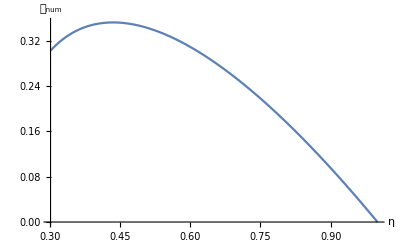

```mathematica
Plot[DangWxl[η] ,{η,ti,t0},WorkingPrecision->30,AxesLabel->{"η","𝒟_num"}]
```

```mathematica
χz[𝓏_]:=(*1/(1+𝓏)^2(1+𝓏-Sqrt[1+𝓏]);*)Evaluate[1/(𝓏+1)(1/(𝒽0 Ωm0^(1/3)ΩΛ^(1/6) 3^(1/4))(EllipticF[ArcCos[(2 Sqrt[3])/(1+Sqrt[3]+((Ωm0/ΩΛ)^(1/3)(1+𝓏)))-1],(2+Sqrt[3])/4]-EllipticF[ArcCos[(2 Sqrt[3])/(1+Sqrt[3]+(Ωm0/ΩΛ)^(1/3))-1],(2+Sqrt[3])/4]))//.{Ωm0->0.3153, ΩΛ->0.6847}];
```

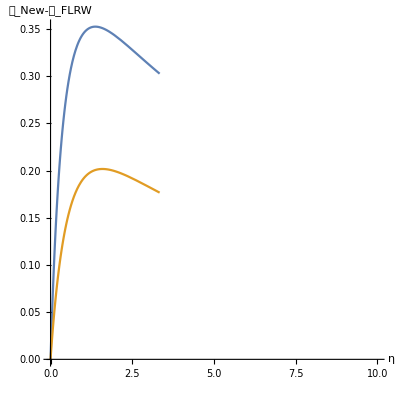

```mathematica
ParametricPlot[{{ZLTB[η], DangWxl[η] },{ZLTB[η],  χz[ZLTB[η]]}},{η,ti,t0},AspectRatio->1, PlotRange->{{0,10}},WorkingPrecision->30,AxesLabel->{"η","𝒟_New-𝒟_FLRW"}]
```

#### Use Sachs focusing equation to compute the D_ang

```mathematica
dlovel[t_]:=(D[ℓ0LTB[p],p]/.p->s)/ℓ0LTB[s]/.s->t
ρLOS[t_]:=ρ[t,r[t]]/.geodesic
```

```mathematica
Timing[solDangLTB=NDSolve[{(da''[t]+dlovel[t]da'[t]==-4π ρLOS[t]da[t]),da[t0]==DangWxl[t0],da'[t0]==Q/ℓ0LTB[t0]}//.param,da,{t,ti,t0},WorkingPrecision->90,PrecisionGoal->90,Method->"StiffnessSwitching",InterpolationOrder->10,MaxSteps->10^10]]
```

NDSolve::precw: The precision of the differential equation ({{(«1» da'[t])/(InterpolatingFunction[{«1»},{«13»},{«1»},{«250»},{«1»}][t])+da''[t]==-(2 da[t])/(3 (-1/5+t+1/Plus[«1»])^(4/3) (-64/3 Power[«2»] Power[«2»] Power[«2»]+Plus[«3»]^(2/3))),da[1]==0.,da'[1]==-1.},{},{},{},{}}) is less than WorkingPrecision (90.).

InterpolatingFunction::dmval: Input value {1.00000000000000000000000000000000000000000000100000000000001414146495510137846491160128365} lies outside the range of data in the interpolating function. Extrapolation will be used.

{143.904,{{da→InterpolatingFunction[{{0.301511344577763622646812066970062425811553504144486690641698376919680422055367622428076673, 1.00000000000000000000000000000000000000000000000000000000000000000000000000000000000000000}}, <>]}}}

```mathematica
DangLTB[η_]=First[da[η]/.solDangLTB];
Precision[DangLTB[ti]]
Now
```

89.7209

Sat 1 May 2021 14:37:48GMT+2.

ParametricPlot::precw: The precision of the argument function ({((«1»[η])^2-1. (InterpolatingFunction[{{«2»}},«3»,{{«2»}}][η])^2)-0,InterpolatingFunction[«1»][η]-0}) is less than WorkingPrecision (60.).

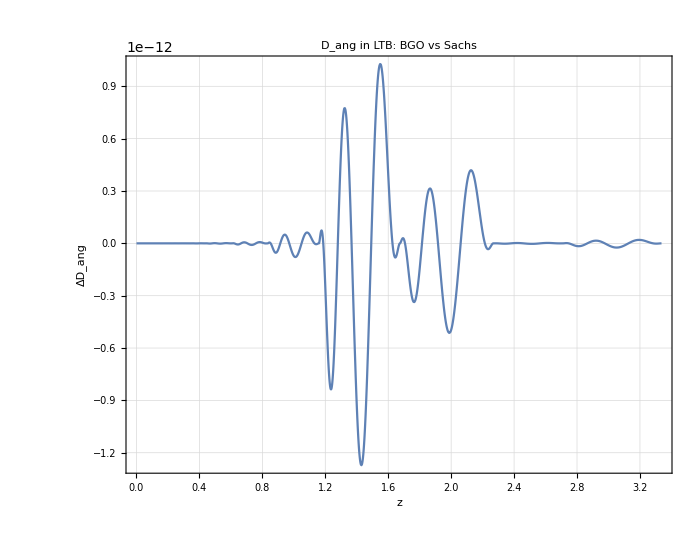

```mathematica
ParametricPlot[{ZN[η],(DangWxl[η]/DangLTB[η]-1)},{η,ti,t0},PlotRange->All,Evaluate[StandardPlotStyle[18,24,"ΔD_ang","z","D_ang in LTB: BGO vs Sachs",{},{}]],AspectRatio->0.8, ImageSize->700,WorkingPrecision->60]
```

### Luminosity distance and Parallax distance and the distance slip

```mathematica
(*𝒲[t_]:=𝒲2[t]*)
```

```mathematica
Timing[tmpWAA=SetPrecision[Table[𝒲[η][[1,1]][[i,j]],{i,2,3},{j,2,3}],50];]
```

{0.007829,Null}

```mathematica
Timing[detWxxAB[t_]=SetPrecision[Evaluate[Simplify[Sqrt[Abs[(Det[tmpWAA])]]]/.η->t],50];]
```

{0.011997,Null}

```mathematica
Dpar[η_]=Evaluate[(gg4[t0].lupN[t0].nup[t0])Evaluate[detWxlAB[η]/detWxxAB[η]]/.Join[param,totN]];
```

```mathematica
ParametricPlot[{{ZN[t],𝒽0 Dpar[t]},{ZN[t],𝒽0 DangWxl[t]}} ,{t,ti,t0},WorkingPrecision->30,ImageSize->700,AspectRatio->0.8,PlotRange->All(*{{0,5},{0,1}}*),Evaluate[StandardPlotStyle[18,24,"D/D_ℋ_0","z","D_par in LTB model",{"D_par^BGO","D_ang^an"},{1,0.5}]]]
```

-Graphics-

```mathematica
Dlum[t_]=(1+ZN[t])^2 DangWxl[t];
```

```mathematica
ParametricPlot[{{ZN[t], 𝒽0 DangWxl[t]},{ZN[t],𝒽0 Dlum[t]},{ZN[t],𝒽0 Dpar[t]}} ,{t,ti,t0},WorkingPrecision->30,ImageSize->700,AspectRatio->0.8,PlotRange->All,Evaluate[StandardPlotStyle[18,24,"D/D_ℋ_0","z","Distances in LTB model",{"D_ang","D_lum","D_par"},{1,0.5}]]]
```

-Graphics-

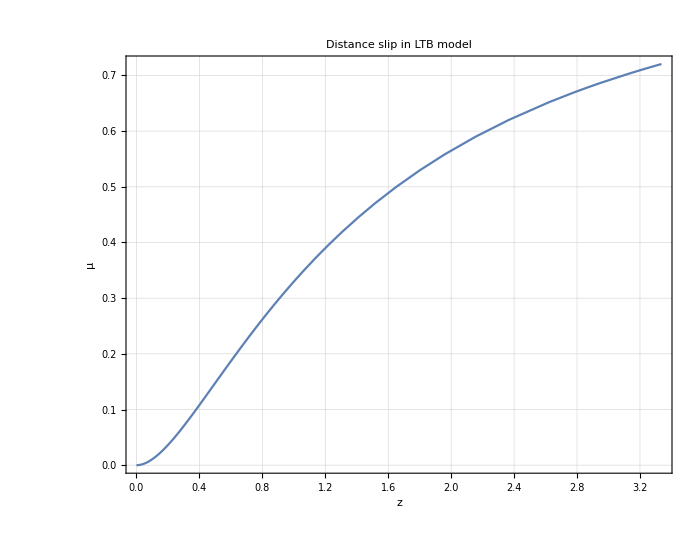

```mathematica
ParametricPlot[{ZN[t], 1-DangWxl[t]^2/Dpar[t]^2},{t,ti,t0},WorkingPrecision->30,ImageSize->700,AspectRatio->0.8,PlotRange->All,Evaluate[StandardPlotStyle[18,24,"μ","z","Distance slip in LTB model",{ },{ }]]]
```

### Redshift drift effects

```mathematica
𝒲XX[η_]:=Mxx/.functional[η];
𝒲LX[η_]:=Mlx/.functional[η];
𝒲XL[η_]:=Mxl/.functional[η];
𝒲LL[η_]:=Mll/.functional[η];
I𝒲XL[η_]:=Inverse[𝒲XL[η]];
```

```mathematica
Uoo[η_]:=-hDD.I𝒲XL[η].𝒲XX[η]
Uoe[η_]:=hDD.I𝒲XL[η]
Ueo[η_]:=-(hDD.𝒲LX[η]-hDD.𝒲LL[η].I𝒲XL[η].𝒲XX[η])
Uee[η_]:= -hDD.𝒲LL[η].I𝒲XL[η]
```

```mathematica
𝒰dd[η_]:= {{Uoo[η],Uoe[η]},{Ueo[η],Uee[η]}}
```

```mathematica
(*four acceleration can be calculated as a^ν==u^μ∇_μ u^ν*)
```

```mathematica
up={1,0,0,0}(*{u0[η],u1[η],u2[η],u3[η]}*);
Table[Sum[(up[[j]]D[up[[i]],X4[[j]]]),{j,1,4}]+Sum[Christoffel[g4,X4][[i,j,s]]up[[j]]up[[s]],{j,1,4},{s,1,4}]//Simplify,{i,1,4}]
```

{0,0,0,0}

```mathematica
e0[s_]=ldownN[s]/Q;
e1[η_]=gg4[η].(Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]])/.totN;
e2[η_]=gg4[η].(Evaluate[Cf2[η]nup[η]+Flatten[{0, P2[η]}]])/.totN;
e3[η_]=(gg4[η].(Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]])+e0[η])/Q/.totN;
```

```mathematica
Clear[up]
```

```mathematica
up[η_]:={e0[η].u[η],e1[η].u[η],e2[η].u[η],e3[η].u[η]}
```

```mathematica
uE[η_]:={e0[η].u[η],e1[η].u[η],e2[η].u[η],e3[η].u[η]}
aE[η_]:={0,0,0,0}
uO[η_]:=u[η]
aO[η_]:={0,0,0,0}
```

```mathematica
ΞDoppler[η_]:=(ldownN[η]/(uE[η].ldownN[η])).(aE[η]/(1+ZN[η]))-(ldownN[t0]/(uO[t0].ldownN[t0])).aO[t0]
lnzdrift[η_]:=(ΞDoppler[η]-1/(uO[t0].ldownN[t0])(Uoo[η].uO[t0].uO[t0]+1/(1+ZN[η])Uoe[η].uO[t0].uE[η]+1/(1+ZN[η])Ueo[η].uE[η].uO[t0]+1/(1+ZN[η])^2 Uee[η].uE[η].uE[η]))/.BGO/.geodesic
```

```mathematica
cL=(299792458 3.24078 10^-23)/L(*c/L==(Mpc/s)/Mpc=1/s*)
```

1.091494704×10^-18

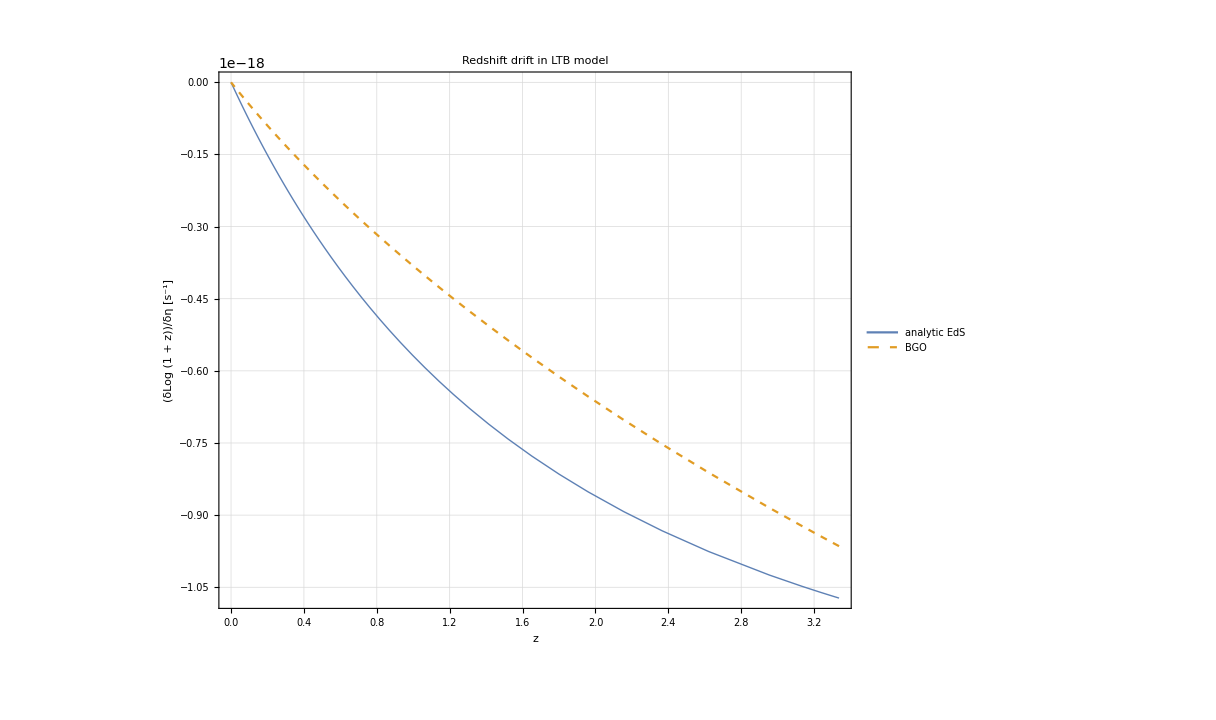

```mathematica
ParametricPlot[{{ZN[t],cL 𝒽0/(1+Zbg[t])((1+Zbg[t])-Sqrt[(1+Zbg[t])^3])/.param},{ZN[t],cL lnzdrift[t]}},{t,ti,t0},ImageSize->900,PlotRange->All,AspectRatio->0.8,PlotStyle->{Thick,Dashed},Evaluate[StandardPlotStyle[20,24,"(δLog (1 + z))/δη [s^-1]","z","Redshift drift in LTB model",{"analytic EdS","BGO" },{0.8,0.8 }]]]
```

Compute the redshift drift using the standard method

ⅆ/ⅆt(δz/(1+z))==(∂_t ∂_t ∂_r R[t,r])/(∂_r R[t,r])δτ_0/(1+z)==-2/9 δτ_0/t^(4/3)

```mathematica
DF[t_,r_]:=D[ℛ[τ,s],τ,τ,s]/D[ℛ[τ,s],s]/.{τ-> t,s->r}
```

```mathematica
(*Aδz[t]=*)AbsoluteTiming[dzlist=Table[{t,NIntegrate[DF[s,r[s]]/(1+ZLTB[s])/.geodesic,{s,t,t0}]},{t,ti,t0,(t0-ti)/9999}];]
```

{111355.,Null}

```mathematica
Aδz=Interpolation[dzlist]
```

InterpolatingFunction[…]

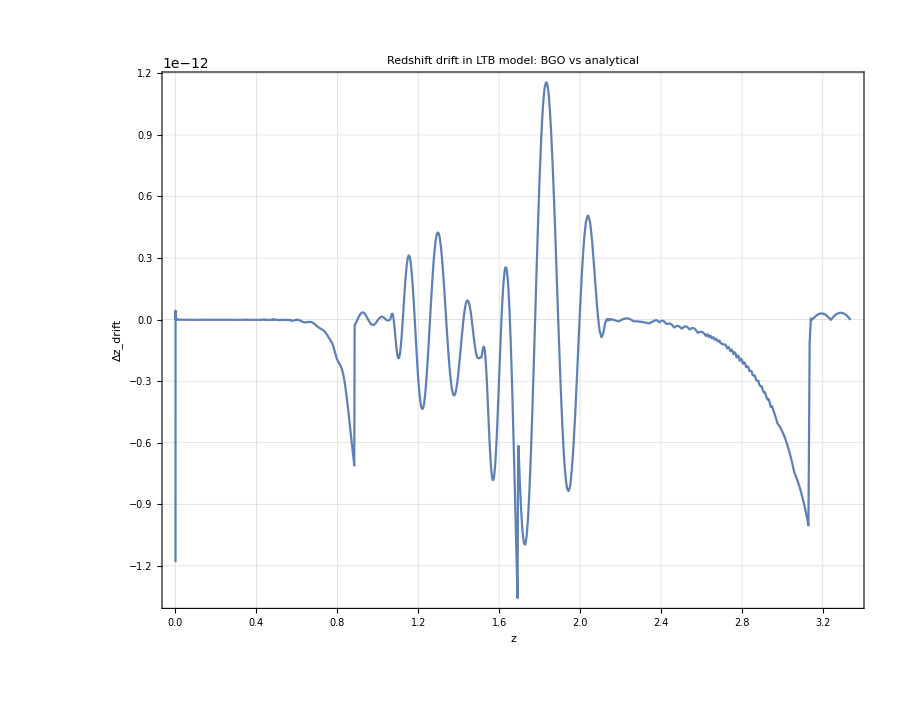

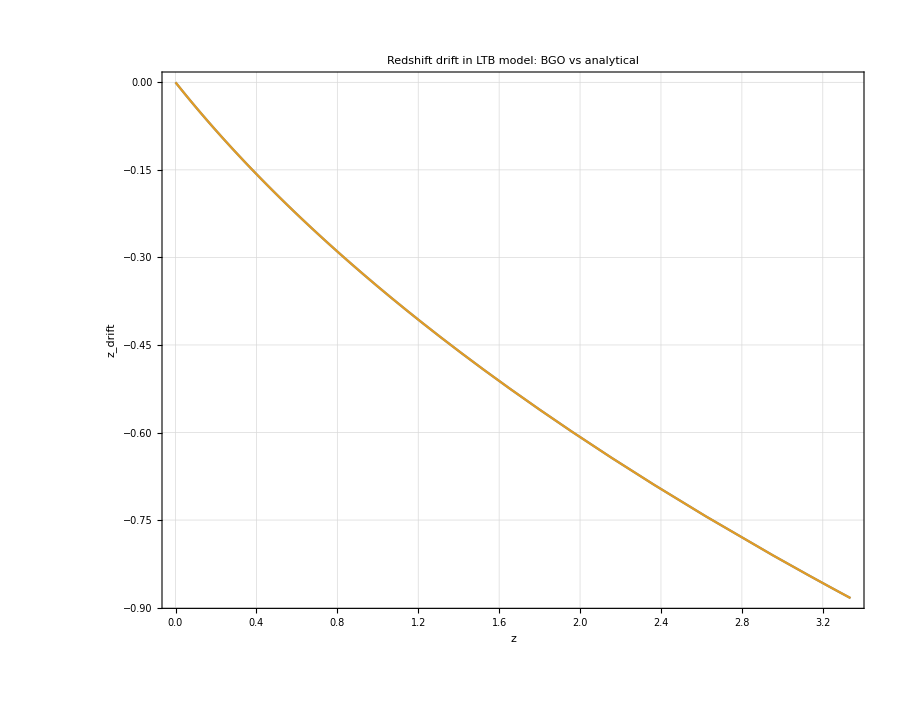

```mathematica
ParametricPlot[{ZN[t],lnzdrift[t]/Aδz[t]-1},{t,ti,t0},ImageSize->900,PlotRange->All,AspectRatio->0.8,WorkingPrecision->60,Evaluate[StandardPlotStyle[20,24,"Δz_drift","z","Redshift drift in LTB model: BGO vs analytical",{},{}]]]
ParametricPlot[{{ZN[t], lnzdrift[t] },{ZN[t], Aδz[t]}},{t,ti,t0},ImageSize->900,PlotRange->All,AspectRatio->0.8,WorkingPrecision->60,Evaluate[StandardPlotStyle[20,24,"z_drift","z","Redshift drift in LTB model: BGO vs analytical",{},{}]]]
```

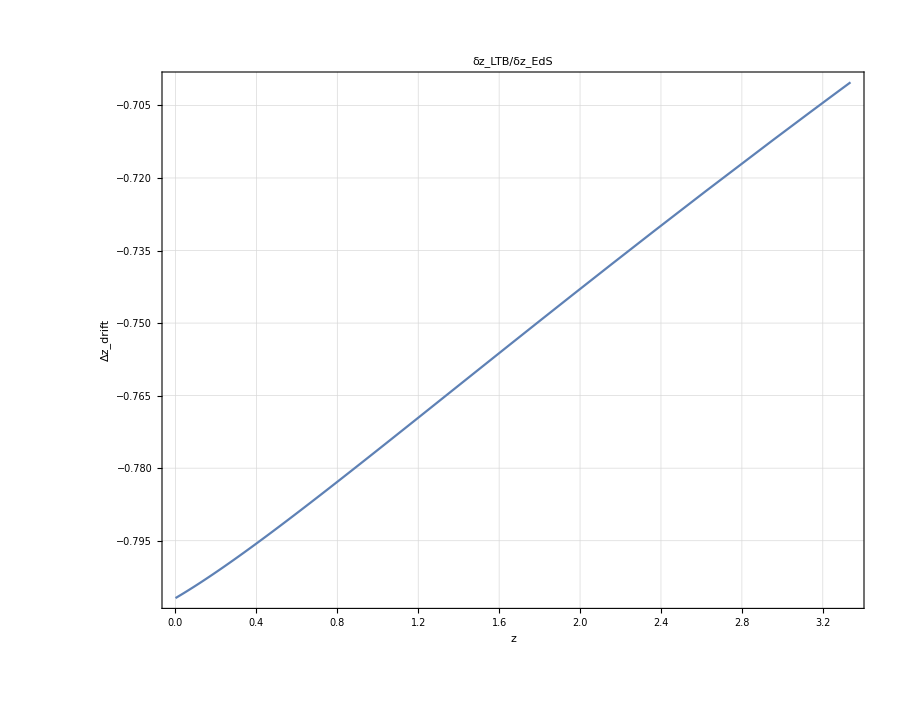

```mathematica
δzEdS[t_]:=𝒽0/(1+Zbg[t])((1+Zbg[t])-Sqrt[(1+Zbg[t])^3])/.param
ParametricPlot[{ZN[t],lnzdrift[t]/δzEdS[t]-1},{t,ti,t0},ImageSize->900,PlotRange->All,AspectRatio->0.8,WorkingPrecision->60,Evaluate[StandardPlotStyle[20,24,"Δz_drift","z","δz_LTB/δz_EdS",{},{}]]]
```

### Position drift

```mathematica
WXX[η_]:=Mxx/.functional[η];
WLX[η_]:=Mlx/.functional[η];
WXL[η_]:=Mxl/.functional[η];
WLL[η_]:=Mll/.functional[η];
IWXL[η_]:=Inverse[WXL[η]];
```

```mathematica
(*IWxlAB[η_]:=Table[IWXL[η][[i,j]],{i,2,3},{j,2,3}];*)

m[η_]:=Table[WXX[η][[i,j]]-KroneckerDelta[i,j],{i, 1,4},{j,1,4}];
```

```mathematica
PTuO[η_]:=Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]/.totBG
PTuO2[η_]:=Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]/.totBG2
```

```mathematica
(PTuO[η]-uO[η])/.η->ETA0//Simplify
(PTuO[η]-uO[η])/.η->ηin//Simplify
(PTuO2[η]-uO[η])/.η->ETA0//Simplify
(PTuO2[η]-uO[η])/.η->ηin//Simplify
```

{0.,0.,0.,0.}

{4.99900005000000000000455780246751407341×10^7,2.4950740937755252394561913066492881894×10^7,-2.50491616956940152479561938663224184059×10^7,-3.53553387057739856268006844359873090119×10^7}

{0.,0.,0.,0.}

{4.9990000500000000000000000000002664748522290551002993543084×10^7,2.4999999750000000000000000000001332374301603282576042793612×10^7,-2.4999999750000000000000000000001332374301603282576042793612×10^7,-3.5355338705773985626768455904822155173624761984823569792842×10^7}

```mathematica
δr[η_]:=Table[((cL L)/(uO[ETA0].ldown[ETA0])(1/(1+redshift[η])Sum[IWXL[η][[indA, indB]]uE[η][[indB]], {indB, 2,3}]-Sum[IWXL[η][[indA, indB]]PTuO[η][[indB]], {indB, 2,3}]-Sum[IWXL[η][[indA, indB]]m[η][[indB, indi]]uO[ETA0][[indi]], {indB, 2,3}, {indi, 1, 3}])+aO[ETA0][[indA]])/.BGO/.geodesic,{indA,2,3}]

δr2[η_]:=Table[(1/(uO[ETA0].ldown2[ETA0])(1/(1+redshift2[η])Sum[IWXL[η][[indA, indB]]uE[η][[indB]], {indB, 2,3}]-Sum[IWXL[η][[indA, indB]]WXX[η][[indB, indi]]uO[ETA0][[indi]], {indB, 2,3}, {indi, 1, 3}])+aO[ETA0][[indA]])/.BGO2/.geodesic2,{indA,2,3}]


(*Usa Wxx e scrivi r^A usando δx=u δτ*)



(*Table[((cL L)/(uO[ETA0].ldown2[ETA0])(1/(1+redshift2[η])Sum[IWXL[η][[indA, indB]]uE[η][[indB]], {indB, 2,3}]-Sum[IWXL[η][[indA, indB]]PTuO2[η][[indB]], {indB, 2,3}]-Sum[IWXL[η][[indA, indB]]m[η][[indB, indi]]uO[ETA0][[indi]], {indB, 2,3}, {indi, 1, 3}])+aO[ETA0][[indA]])/.BGO2/.geodesic2,{indA,2,3}]*)
```

```mathematica
(*δr[η_]:=Table[(1/(uO[ETA0].ldown[ETA0])(1/(1+redshift[η])Sum[IWXL[η][[indA, indB]]uE[η][[indB]], {indB, 2,3}]-Sum[IWXL[η][[indA, indB]]WXX[η][[indB, indi]]uO[ETA0][[indi]], {indB, 2,3}, {indi, 1, 3}])+aO[ETA0][[indA]])/.BGO/.geodesic,{indA,2,3}]*)
```

```mathematica
rA[η_, τ_]:=Table[(1/(uO[ETA0].ldown2[ETA0])(1/(1+redshift2[η])Sum[IWXL[η][[indA, indB]]uE[η][[indB]]τ, {indB, 2,3}]-Sum[IWXL[η][[indA, indB]]WXX[η][[indB, indi]]uO[ETA0][[indi]] τ, {indB, 2,3}, {indi, 1, 3}])+aO[ETA0][[indA]] τ)/.BGO2/.geodesic2,{indA,2,3}]
```

{0,0}

```mathematica
rA[0.7, 10]
```

{0,0}

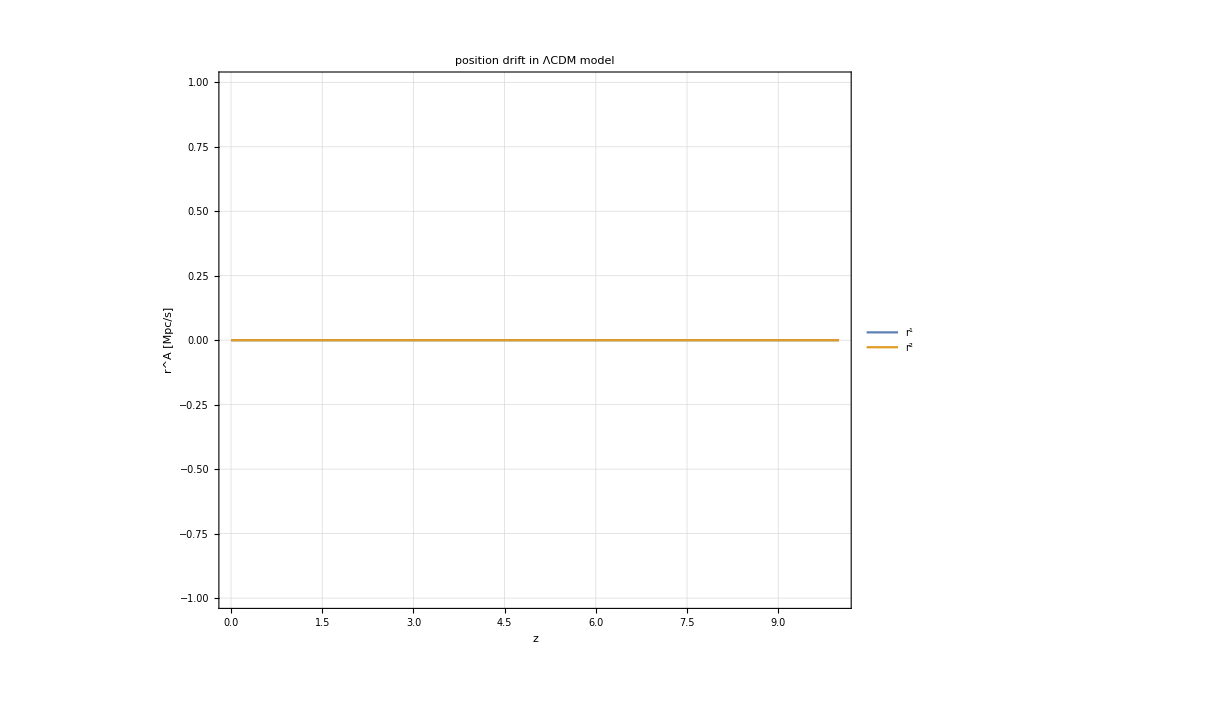

```mathematica
ParametricPlot[{{redshift2[t], rA[t, 10][[1]]},{redshift2[t], rA[t, 10][[2]]}},{t,tz10,ETA0},ImageSize->900,PlotRange->All(*{{-0.4, 10.4},{-10^-30,10^-30}}*),AspectRatio->0.8,Evaluate[StandardPlotStyle[20,24,"r^A [Mpc/s]","z","position drift in ΛCDM model",{"r^1","r^2"},{0.8,0.8}]]]
```

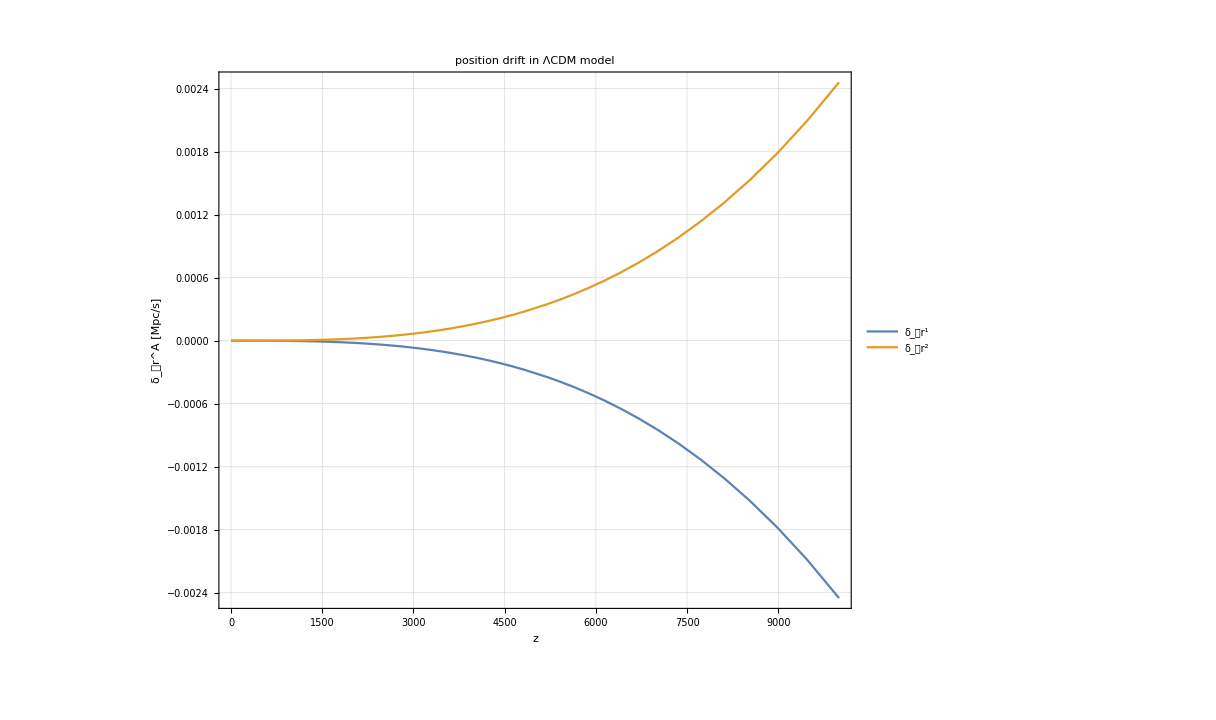

```mathematica
ParametricPlot[{{redshift[t], δr[t][[1]]},{redshift[t], δr[t][[2]]}},{t,ηin,ETA0},ImageSize->900,PlotRange->All(*{{-0.4, 10.4},{-10^-30,10^-30}}*),AspectRatio->0.8,Evaluate[StandardPlotStyle[20,24,"δ_𝒪r^A [Mpc/s]","z","position drift in ΛCDM model",{"δ_𝒪r^1","δ_𝒪r^2"},{0.8,0.8}]]]
(*ParametricPlot[{redshift[t],lnzdrift[t]/ANALITICzdrift[t]-1},{t,ηin,ETA0},ImageSize->900,PlotRange->{{0,10},{-2.5 10^-24,2.5 10^-24}},AspectRatio->0.8,WorkingPrecision->10000,Evaluate[StandardPlotStyle[20,24,"Δz_drift","z","Redshift drift in ΛCDM model: BGO vs analytical",{},{}]]]
Graphics[{White,Rectangle[{0,0},{1,1}]}]*)
```

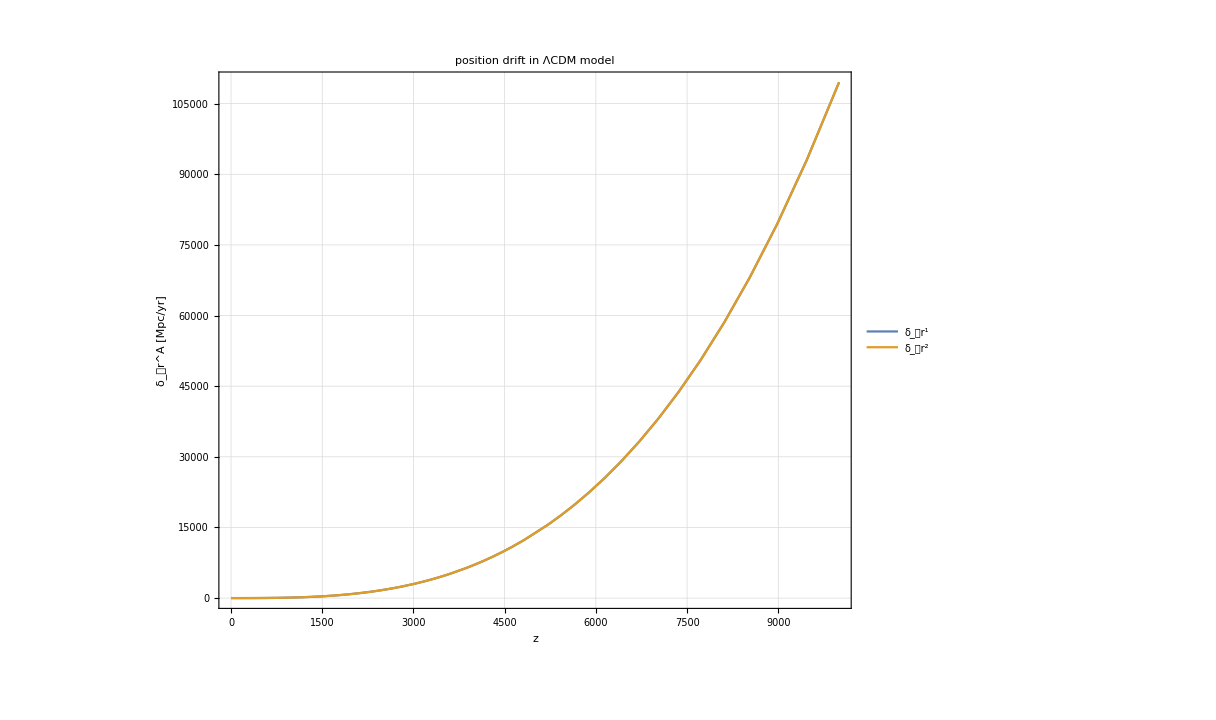

```mathematica
ParametricPlot[{{redshift[t], Norm[ 1/(3.17098 10^-8) δr[t]]},{redshift2[t], Norm[ 1/(3.17098 10^-8) δr2[t]]}},{t,ηin,ETA0},ImageSize->900,PlotRange->All(*{{0, 10},{-2 10^-4,2 10^-4}}*),AspectRatio->0.8,Evaluate[StandardPlotStyle[20,24,"δ_𝒪r^A [Mpc/yr]","z","position drift in ΛCDM model",{"δ_𝒪r^1","δ_𝒪r^2"},{0.8,0.5}]]]
```

```mathematica
ParametricPlot[{redshift[t],radTOarcsec Norm[ 1/(3.17098 10^-8) δr[t]]},{t,ηin,ETA0},ImageSize->900,PlotRange->{{0, 10},{-2 10^-4,2 10^-4}},AspectRatio->0.8,Evaluate[StandardPlotStyle[20,24,"δ_𝒪r^A [Mpc/yr]","z","position drift in ΛCDM model",{"δ_𝒪r^1","δ_𝒪r^2"},{0.8,0.5}]]]
```

-Graphics-

```mathematica
(1/(3.17098 10^-8)δr[tz1][[1]])/((1+redshift[tz1])L DangWxl[tz1])
```

-5.721929582973952756065797844637067465123164214919×10^-10

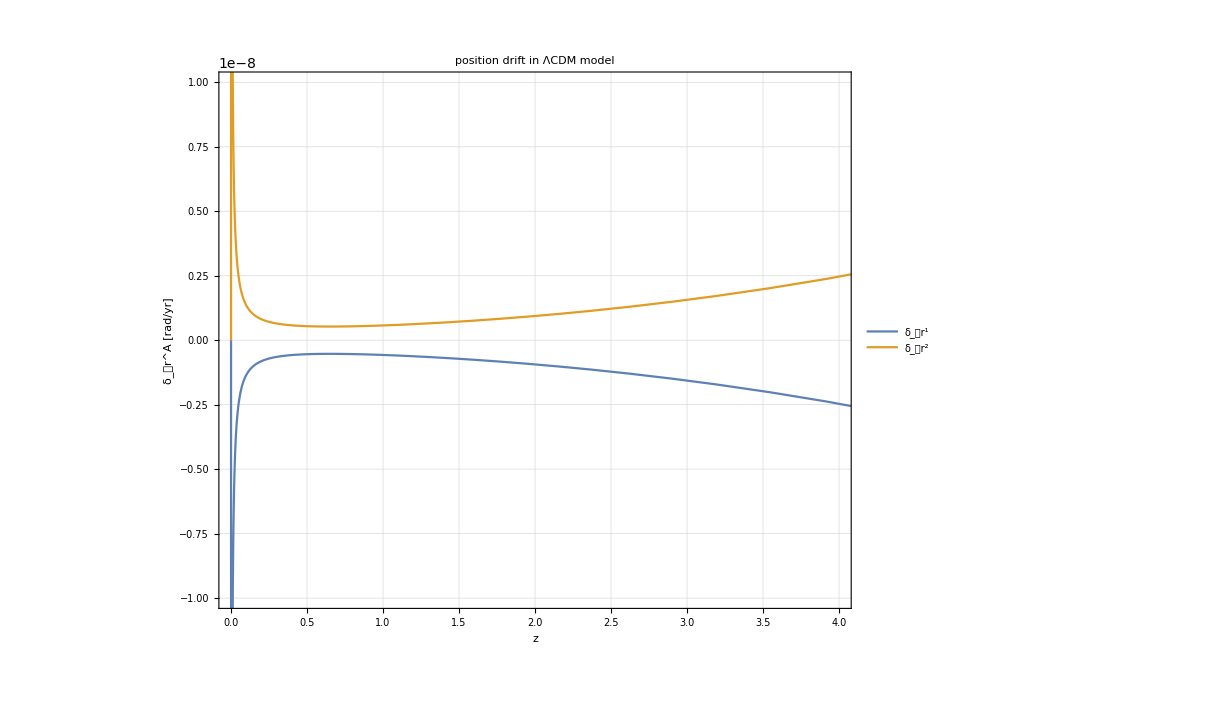

```mathematica
ParametricPlot[{{redshift[t], (1/(3.17098 10^-8)δr[t][[1]])/((1+redshift[t])L DangWxl[t])},{redshift[t],(1/(3.17098 10^-8)δr[t][[2]])/((1+redshift[t])L DangWxl[t])}},{t,ηin,ETA0},ImageSize->900,PlotRange->{{0, 4},{-10^-8,10^-8}},AspectRatio->0.8,Evaluate[StandardPlotStyle[20,24,"δ_𝒪r^A [rad/yr]","z","position drift in ΛCDM model",{"δ_𝒪r^1","δ_𝒪r^2"},{0.8,0.5}]]]
```

```mathematica
radTOarcsec Norm[ (1/(3.17098 10^-8)δr[tz1])/((1+redshift[tz1])L DangWxl[tz1])]
```

0.0001669101086558926008978003771228592589880664869077

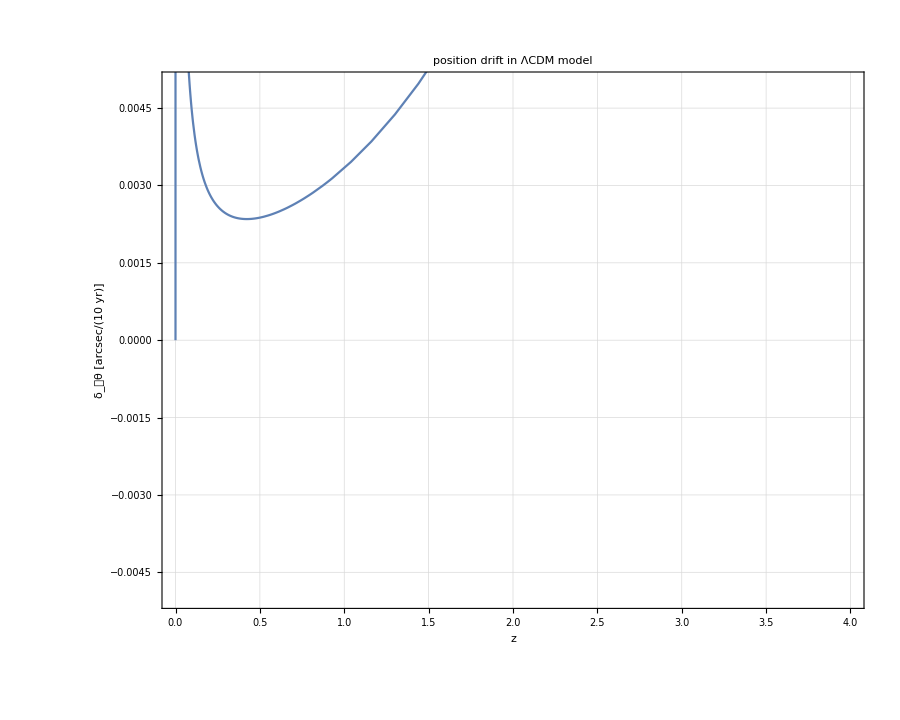

```mathematica
ParametricPlot[{redshift[t],radTOarcsec Norm[ (1/(3.17098 10^-8)δr[t]10)/(L DangWxl[t])]},{t,ηin,ETA0},ImageSize->900,PlotRange->{{0, 4},{-5 10^-3,5 10^-3}},AspectRatio->0.8,Evaluate[StandardPlotStyle[20,24,"δ_𝒪θ [arcsec/(10  yr)]","z","position drift in ΛCDM model",{ },{0.8,0.5}]]]
```

```mathematica
PTuO[η_]:=Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]/.totBG
PTf1[η_]:=Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]/.totBG
PTf2[η_]:=Evaluate[Cf1[η]nup[η]+Flatten[{0, P2[η]}]]/.totBG

PTuO2[η_]:=Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]/.totBG2
PTf12[η_]:=Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]/.totBG2
PTf22[η_]:=Evaluate[Cf1[η]nup[η]+Flatten[{0, P2[η]}]]/.totBG2
```

```mathematica
𝓀𝓊[η_]:=Evaluate[(gg4[η].PTuO2[η].k[η]/.totBG2)]
r[η_]:={(*1/𝓀𝓊[η](gg4[η].lup2[η].k[η])/Q2+1,*)(gg4[η].PTf12[η].k[η])/𝓀𝓊[η],(gg4[η].PTf22[η].k[η])/𝓀𝓊[η](*,1/𝓀𝓊[η]((gg4[η].lup2[η].k[η])/Q2^2+(gg4[η].PTuO2[η].k[η])/Q2)*)}/.totBG2
r0[η_]:={(*1,*) 0,0(*, 1/Q2*)}(*δr2*)
```

```mathematica
r[ETA0]
```

{0.0011359057738634843750835995841722485,0.00080439304361187494177653171466906458}

```mathematica
1/(60 60 24 3650)//N
```

3.17098×10^-9

```mathematica
δθ[η_]:=-(1/(3.1709791983764586*^-9)δr[η].r0[η]+r[η].(δr2[η]/(3.1709791983764586*^-9)))/Sqrt[1-(r0[η].r[η])^2](*δθ[η_,δτ_]:=ArcTan[(1/(3.17098 10^-8)δr[η] δτ)/((1+redshift[η])L DangWxl[η])]*)
```

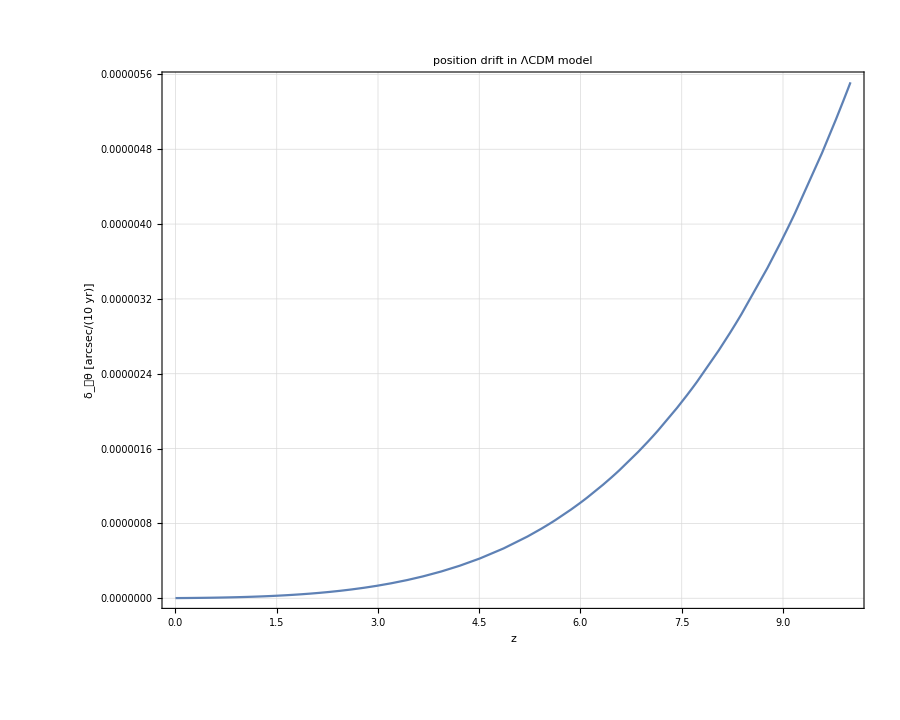

```mathematica
ParametricPlot[{redshift[t],  δθ[t]},{t,tz10,ETA0},ImageSize->900,PlotRange->All,AspectRatio->0.8,Evaluate[StandardPlotStyle[20,24,"δ_𝒪θ [arcsec/(10  yr)]","z","position drift in ΛCDM model",{ },{0.8,0.5}]]]
```

```mathematica
Dist=Norm[trajectoryBG[tz10]-trajectoryBG2[tz10]]L
```

13.41236192126456

```mathematica
ℐ[z_]:=Evaluate[(1/(Ωm0^(1/3)ΩΛ^(1/6) 3^(1/4))(EllipticF[ArcCos[(2 Sqrt[3])/(1+Sqrt[3]+((Ωm0/ΩΛ)^(1/3)(1+z)))-1],(2+Sqrt[3])/4]-EllipticF[ArcCos[(2 Sqrt[3])/(1+Sqrt[3]+(Ωm0/ΩΛ)^(1/3))-1],(2+Sqrt[3])/4]))//.param];
```

```mathematica
δθp[η_]:=68.755Dist((1+redshift2[η]+lnzdrift2[η])/ℐ[redshift2[η]+lnzdrift2[η]]-(1+redshift2[η])/ℐ[redshift2[η]])
```

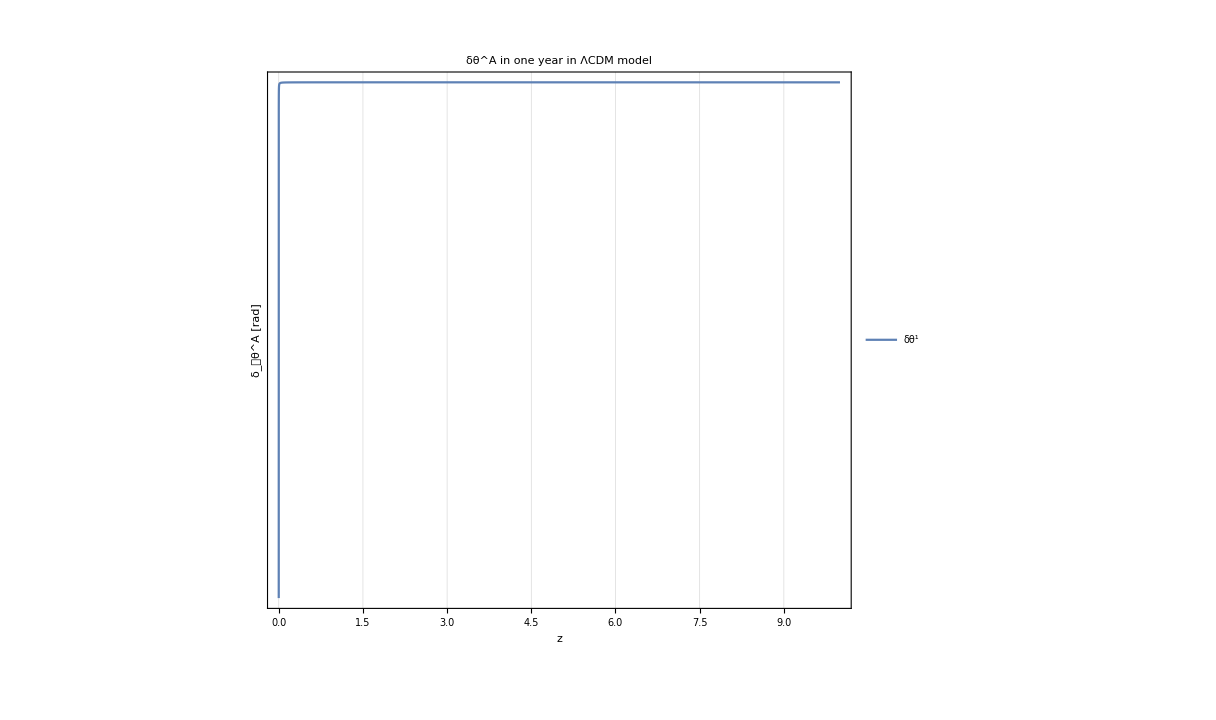

```mathematica
ParametricPlot[{redshift2[t], δθp[t]},{t,tz10,ETA0},ImageSize->900,PlotRange->All,AspectRatio->0.8,ScalingFunctions->{Identity,"Log"},Evaluate[StandardPlotStyle[20,24,"δ_𝒪θ^A [rad]","z","δθ^A in one year in ΛCDM model",{"δθ^1","δθ^2"},{0.8,0.5}]]]
```

```mathematica
ParametricPlot[{{redshift[t], δθ[t,1][[1]]},{redshift[t],δθ[t,1][[2]]}},{t,ηin,ETA0},ImageSize->900,PlotRange->{{-0.5, 1100.5},{-0.008, 0}},AspectRatio->0.8,Evaluate[StandardPlotStyle[20,24,"δ_𝒪θ^A [rad]","z","δθ^A in one year in ΛCDM model",{"δθ^1","δθ^2"},{0.8,0.5}]]]
```

$Aborted

```mathematica
tz1=t/.Solve[redshift[t]==1, t][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

0.7639506593534118814092277264122331894891017415881816057481

```mathematica
D[ArcTan[x],x]
```

1/(1+x^2)

```mathematica
radTOarcsec=(3600×180)/π
```

648000/π

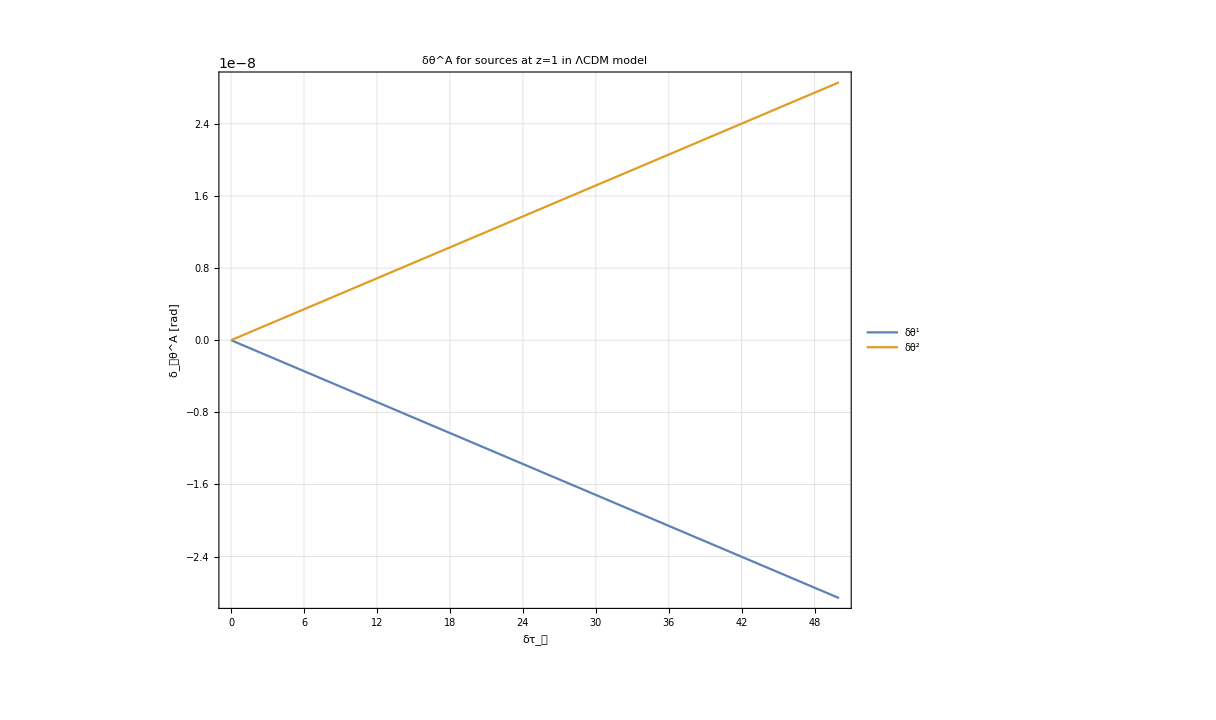

```mathematica
Plot[{ δθ[tz1,t][[1]],δθ[tz1,t][[2]]},{t,0,50},ImageSize->900,PlotRange->All(*{{-0.4, 10.4},{-10^-30,10^-30}}*),AspectRatio->0.8,Evaluate[StandardPlotStyle[20,24,"δ_𝒪θ^A [rad]","δτ_𝒪","δθ^A for sources at z=1 in ΛCDM model",{"δθ^1","δθ^2"},{0.8,0.5}]]]
```

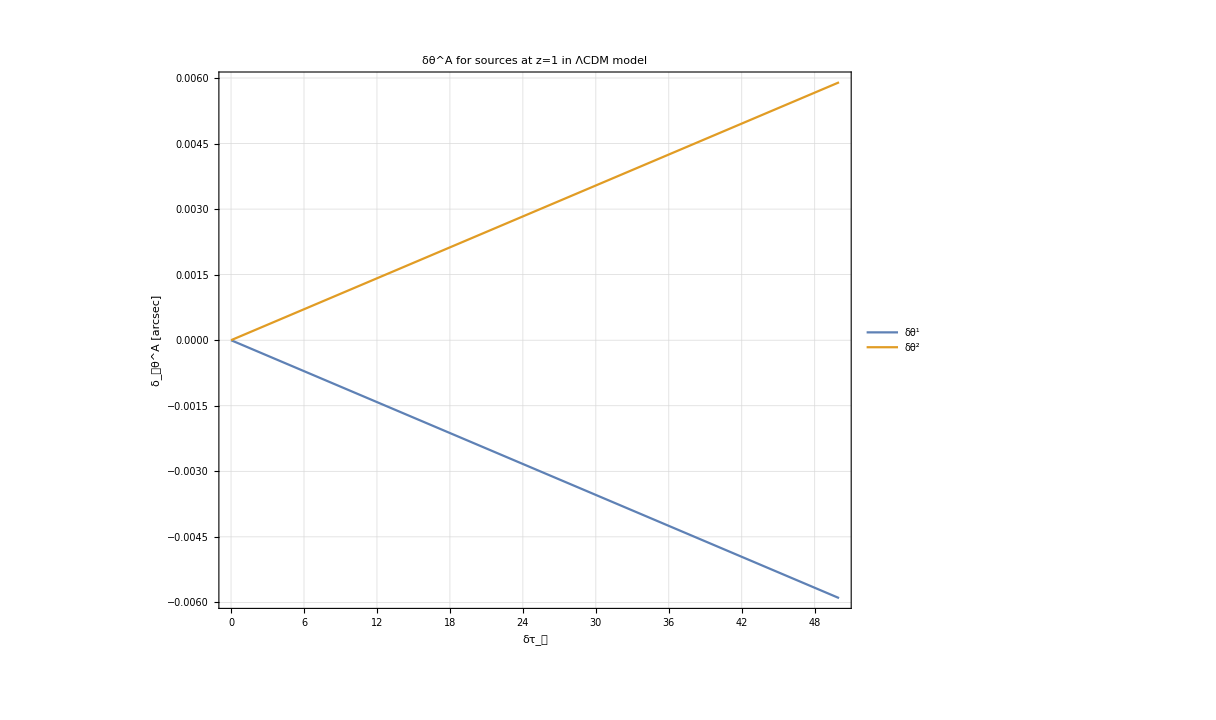

```mathematica
Plot[{ radTOarcsec δθ[tz1,t][[1]],radTOarcsec δθ[tz1,t][[2]]},{t,0,50},ImageSize->900,PlotRange->All(*{{-0.4, 10.4},{-10^-30,10^-30}}*),AspectRatio->0.8,Evaluate[StandardPlotStyle[20,24,"δ_𝒪θ^A [arcsec]","δτ_𝒪","δθ^A for sources at z=1 in ΛCDM model",{"δθ^1","δθ^2"},{0.8,0.5}]]]
```

```mathematica
observ[rA_, ti_, tf_,bin_, z_]:=Module[{tz, τ},
tz=τ/.Solve[redshift[τ]==1, τ][[1]];
 Table[{t, rA+1/(3.17098 10^-8)δr[tz]t}, {t, ti, tf, bin}]]
```

```mathematica
Oz1=observ[{0,0}, 0, 10, 1, 10]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{0,{0,0}},{1,{-1.94699670915040178083033295336987236282771882486227480946×10^-6,1.94699670915040178083033295336987236282771882486227480946×10^-6}},{2,{-3.89399341830080356166066590673974472565543764972454961893×10^-6,3.89399341830080356166066590673974472565543764972454961893×10^-6}},{3,{-5.84099012745120534249099886010961708848315647458682442839×10^-6,5.84099012745120534249099886010961708848315647458682442839×10^-6}},{4,{-7.78798683660160712332133181347948945131087529944909923786×10^-6,7.78798683660160712332133181347948945131087529944909923786×10^-6}},{5,{-9.73498354575200890415166476684936181413859412431137404732×10^-6,9.73498354575200890415166476684936181413859412431137404732×10^-6}},{6,{-0.0000116819802549024106849819977202192341769663129491736488568,0.0000116819802549024106849819977202192341769663129491736488568}},{7,{-0.0000136289769640528124658123306735891065397940317740359236663,0.0000136289769640528124658123306735891065397940317740359236663}},{8,{-0.0000155759736732032142466426636269589789026217505988981984757,0.0000155759736732032142466426636269589789026217505988981984757}},{9,{-0.0000175229703823536160274729965803288512654494694237604732852,0.0000175229703823536160274729965803288512654494694237604732852}},{10,{-0.0000194699670915040178083033295336987236282771882486227480946,0.0000194699670915040178083033295336987236282771882486227480946}}}

```mathematica
Length[Oz1]
```

11

```mathematica
Animate[Graphics[{Arrow[{Oz1[[1,2]],Oz1[[i,2]]}], Red, Arrow[{Oz1[[1,2]],Oz1[[2,2]]}]},Frame->True, ImageSize->400,AxesLabel->{"e^1 [Mpc]","e^2 [Mpc]"},AxesStyle->Directive[Black,12], PlotRange->{{-0.00002,10^-6},{-10^-6,0.00002}}],{i, 2, Length[Oz1],1}, AnimationRunning->False]
```

F

```mathematica
PTuO[η_]:=Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]/.totBG
PTf1[η_]:=Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]/.totBG
PTf2[η_]:=Evaluate[Cf1[η]nup[η]+Flatten[{0, P2[η]}]]/.totBG

PTuO2[η_]:=Evaluate[Cu[η]nup[η]+Flatten[{0, Pu[η]}]]/.totBG2
PTf12[η_]:=Evaluate[Cf1[η]nup[η]+Flatten[{0, P1[η]}]]/.totBG2
PTf22[η_]:=Evaluate[Cf1[η]nup[η]+Flatten[{0, P2[η]}]]/.totBG2
```

```mathematica
CF0[η_]:=ldown2[η]/Q2/.totBG2
CF1[η_]:=gg4[η].PTf12[η]/.totBG2
CF2[η_]:=gg4[η].PTf22[η]/.totBG2
CF3[η_]:=((gg4[η].PTuO2[η])/Q2+ldown2[η]/Q2^2)/.totBG2
```

```mathematica
𝒻={𝓊, 𝒻𝒻1, 𝒻𝒻2, ℓ}
𝒸𝒻={{0,0,0,1/𝒬},{0,1,0,0},{0,0,1,0},{1/𝒬,0,0,1/𝒬^2}}.𝒻
```

{𝓊,𝒻𝒻1,𝒻𝒻2,ℓ}

{ℓ/𝒬,𝒻𝒻1,𝒻𝒻2,ℓ/𝒬^2+𝓊/𝒬}

```mathematica
(𝓀.𝒸𝒻)/(𝓀 𝓊)+𝓊.𝒸𝒻
{(𝓀.ℓ)/𝒬,𝓀.𝒻𝒻1,𝓀.𝒻𝒻2,(𝓀.ℓ)/𝒬^2+(𝓀.𝓊)/𝒬}/(𝓀 𝓊)+{(𝓊.ℓ)/𝒬,𝓊.𝒻𝒻1,𝓊.𝒻𝒻2,(𝓊.ℓ)/𝒬^2+(𝓊.𝓊)/𝒬}==1/(𝓀 𝓊){(𝓀.ℓ)/𝒬,𝓀.𝒻𝒻1,𝓀.𝒻𝒻2,(𝓀.ℓ)/𝒬^2+(𝓀.𝓊)/𝒬}+{𝒬/𝒬,0,0,𝒬/𝒬^2+-1/𝒬}=={1/(𝓀 𝓊)(𝓀.ℓ)/𝒬+1,(𝓀.𝒻𝒻1)/(𝓀 𝓊),(𝓀.𝒻𝒻2)/(𝓀 𝓊),1/(𝓀 𝓊)((𝓀.ℓ)/𝒬^2+(𝓀.𝓊)/𝒬)}
```

(𝓀.{ℓ/𝒬,𝒻𝒻1,𝒻𝒻2,ℓ/𝒬^2+𝓊/𝒬})/(𝓀 𝓊)+𝓊.{ℓ/𝒬,𝒻𝒻1,𝒻𝒻2,ℓ/𝒬^2+𝓊/𝒬}

```mathematica
𝓀𝓊[η_]:=Evaluate[(gg4[η].PTuO2[η].k[η]/.totBG2)]
r[η_]:={1/𝓀𝓊[η](gg4[η].lup2[η].k[η])/Q2+1,(gg4[η].PTf12[η].k[η])/𝓀𝓊[η],(gg4[η].PTf22[η].k[η])/𝓀𝓊[η],1/𝓀𝓊[η]((gg4[η].lup2[η].k[η])/Q2^2+(gg4[η].PTuO2[η].k[η])/Q2)}/.totBG2
```

### Shear and expansion

```mathematica
Timing[tmpWllAB=SetPrecision[Table[𝒲[η][[2,2]][[i,j]],{i,2,3},{j,2,3}],50];]
IWxlAB=Inverse[tmpWAB];
```

{748.61,Null}

```mathematica
trxlll[t_]=SetPrecision[Evaluate[Tr[IWxlAB.tmpWllAB]/.η->t],50];
```

```mathematica
DDang[t_]=1/2 DangWxl[t] trxlll[t];
```

```mathematica
𝒮[t_]=Evaluate[(tmpWllAB.IWxlAB)//.η->t];
```

```mathematica
expansion[η_]=Tr[𝒮[η]]/2;
shear[η_]=Sqrt[(Tr[𝒮[η].𝒮[η]]/2-(Tr[𝒮[η]]/2)^2)];
```

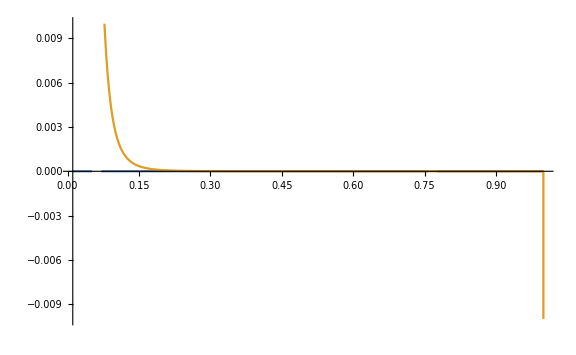

```mathematica
Plot[{shear[η],expansion[η]},{η,ηin,ETA0},ImageSize->Large,PlotRange->0.01]
```

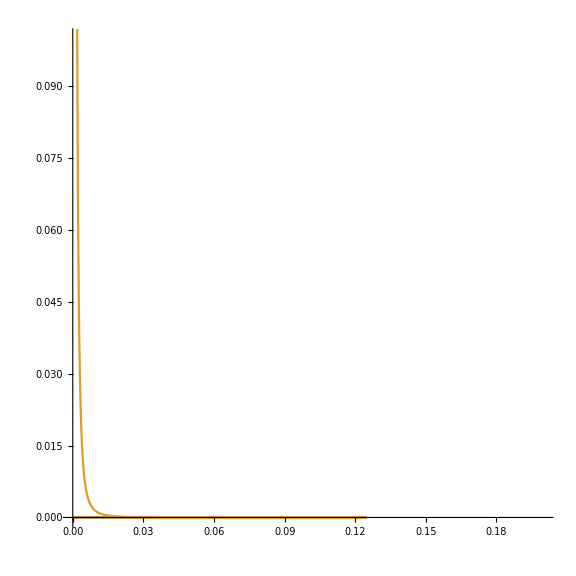

```mathematica
ParametricPlot[{{DangWxl[η], shear[η]},{DangWxl[η],expansion[η]}},{η,ηin,ETA0},ImageSize->Large,PlotRange->{{0,0.2},{0,0.1}}(*{{DangWxl[ETA0], DangWxl[ηin]},{-1,1}}*),AspectRatio->1]
```

```mathematica
δx={0,0,-10^-6/8,-10^-6/8};
δXf[t_]=𝒲[t][[1,2]].δx;
```

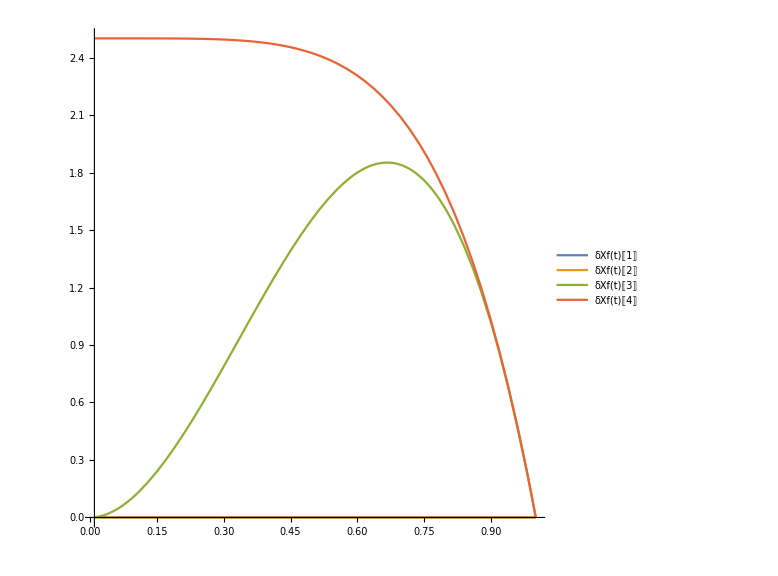

```mathematica
Plot[{δXf[t][[1]],δXf[t][[2]],δXf[t][[3]],δXf[t][[4]]},{t,ηin,ETA0},ImageSize->Large,AspectRatio->1,PlotLegends->"Expressions"]
```

```mathematica
δX0[t_]=(F0[t]/αα[t]).δXf[t]/.Join[param,totBG];
δX1[t_]=(F[t][[1]]-F0[t](ββ[t][[1]])/αα[t]).δXf[t]/.Join[param,totBG];
δX2[t_]=(F[t][[2]]-F0[t](ββ[t][[2]])/αα[t]).δXf[t]/.Join[param,totBG];
δX3[t_]=(F[t][[3]]-F0[t](ββ[t][[3]])/αα[t]).δXf[t]/.Join[param,totBG];
```

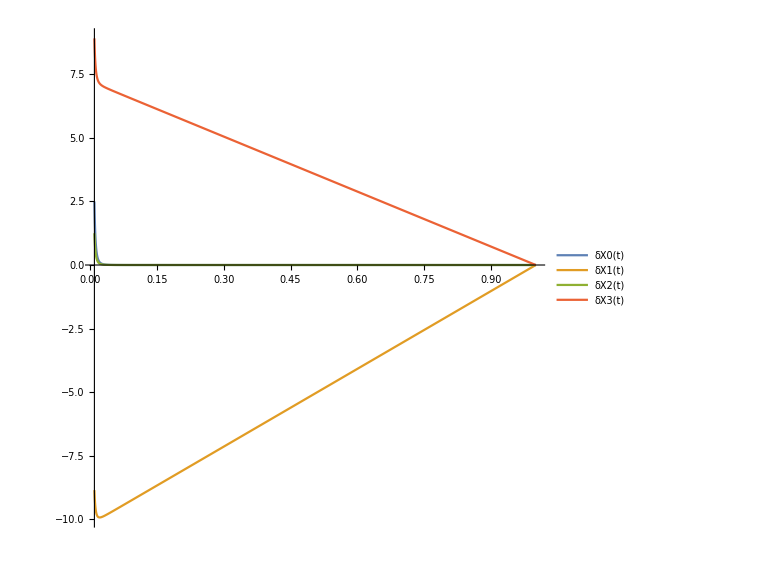

```mathematica
Plot[{δX0[t],δX1[t],δX2[t],δX3[t]},{t,ηin,ETA0},ImageSize->Large,AspectRatio->1,PlotLegends->"Expressions"]
```

```mathematica
Δx[t_]=-{δX0[t],δX1[t],δX2[t],δX3[t]}.ndown[t]/.Join[param,totBG];
ξ[t_]=({δX0[t],δX1[t],δX2[t],δX3[t]}-Δx[t]nup[t])/.Join[param,totBG];
```

```mathematica
Δx[ηin]
ξ[ηin]
```

0.000249999999975000122693

{0,-8.854145189105590659552,1.24999999987500061346,8.912476534011198821003}

```mathematica
δXc[t_]={ξ[t][[2]],ξ[t][[3]],ξ[t][[4]]};
trajectory[t_]=Evaluate[{x[t],y[t],z[t]}/.totBG];
Show[ParametricPlot3D[trajectory[η],{η,ηin,ETA0},PlotRange->{{-1,1},{-1,1},{-1,1}}](*/.Line[x_]:>Sequence[Arrowheads[Table[.02,{100/10}]],Arrow@Line[x]]*) ,Table[Graphics3D[{(*{Opacity[η/300+0.28],Black,Arrowheads[0.02],Arrow[{trajectory[η],(trajectory[η]+40(Pu[η]/.totBG))}]},{Opacity[η/300+0.28],Green,Arrowheads[0.02],Arrow[{trajectory[η],(trajectory[η]+40(P1[η]/.totBG))}]},{Opacity[η/300+0.28],Blue,Arrowheads[0.02],Arrow[{trajectory[η],(trajectory[η]+40(P2[η]/.totBG))}]},{*)(*Opacity[η/300+0.28],*)Red,Arrowheads[0.01],Arrow[{trajectory[η],(trajectory[η]+1/10(δXc[η]/.totBG))}]}],{η,ηin,ETA0,(ETA0-ηin)/30}] , ImageSize->700,AxesLabel->{Style["x/(M̄)",Large],Style["y/(M̄)",Large],Style["z/(M̄)",Large]},AxesStyle->Directive[Black,12],Boxed->False,ViewPoint->{0,100,10}]
```

-Graphics3D-